# Modeling HIV transmission in the Dutch Caribbean D. García-García and G.Rozhnova (in collaboration with M. Hofstra)

## Clearing memory Set your working directory here! NB! Pay attention at specifying the path. It matters whether you use a Mac OS or a Windows OS. My path is for the Windows OS.

```mathematica
$HistoryLength=0;
ClearSystemCache[]
ClearAll["Global`*"]
Clear["Subscript"]
Clear["Superscript"]
Clear["Subsuperscript"]
Memory:=Row[{"Memory Used:",MemoryInUse[]/1024^2.," MB"}]
SetDirectory["/Users/gannarozhnova/Documents/Work/People/David/HIVCaribbean/notebooks/"];
Memory
```

Memory Used:66.6427 MB

## Importing data on demography and migration rates We group migrant population data according to the following groupings: • Locations of interest: Aruba, BES, Curacao. • Interacting regions: Latin America (comprising Central and Southern America), rest of Caribbean (comprising the Caribbean countries except the locations of interest), Netherlands, and rest of the world.

```mathematica
Print[Style["Imported demography",18,Orange,"Text"]];

Print[Style["Imported demography for ABC and interacting regions (full model)",18,Orange,"Text"]];
MigPop=Import["/Users/gannarozhnova/Documents/Work/People/David/HIVCaribbean/data/all_locations/mig_pop_adj.csv"];
MigPop//TableForm

Print[Style["Imported migration rates 2015 2020 adjusted (full model)",18,Orange,"Text"]];
MigRates=Import["/Users/gannarozhnova/Documents/Work/People/David/HIVCaribbean/data/all_locations/mig_rates_adj_2020.xlsx"]⟦1⟧;
MigRates//TableForm

MigPopData=MigPop;
MigRatesData=MigRates;
Print[Style["Migration rates are expressed in units 1/year (full model)",18,Orange,"Text"]];
MigRatesData⟦2;;,3⟧=MigRatesData⟦2;;,3⟧/5;
```

Imported demography

Imported demography for ABC and interacting regions (full model)

| dest_code | dest_name | orig_code | orig_name | y2010 | y2015 | y2020 | v2020 | v2015
1 | 528 | Netherlands* | 528 | Netherlands* | 14784607 | 14770929 | 14667013 | -103916 | -13678
2 | 531 | Curaçao* | 528 | Netherlands* | 8746 | 9504 | 10562 | 1058 | 758
3 | 533 | Aruba* | 528 | Netherlands* | 4359 | 4585 | 5128 | 543 | 226
4 | 535 | Bonaire, Sint Eustatius and Saba* | 528 | Netherlands* | 1907 | 2880 | 3486 | 606 | 973
5 | LAT | LATIN AMERICA | 528 | Netherlands* | 11770 | 13400 | 15216 | 1816 | 1630
6 | OTH | OTHER | 528 | Netherlands* | 827324 | 837385 | 937237 | 99852 | 10061
7 | ROC | REST OF CARIBBEAN | 528 | Netherlands* | 2189 | 2219 | 2260 | 41 | 30
8 | 528 | Netherlands* | 531 | Curaçao* | 0 | 280 | 1259 | 979 | 280
9 | 531 | Curaçao* | 531 | Curaçao* | 124750 | 123820 | 122079 | -1741 | -930
10 | 533 | Aruba* | 531 | Curaçao* | 2335 | 2455 | 2745 | 290 | 120
11 | 535 | Bonaire, Sint Eustatius and Saba* | 531 | Curaçao* | 3216 | 3540 | 3909 | 369 | 324
12 | LAT | LATIN AMERICA | 531 | Curaçao* | 865 | 917 | 899 | -18 | 52
13 | OTH | OTHER | 531 | Curaçao* | 520 | 618 | 665 | 47 | 98
14 | ROC | REST OF CARIBBEAN | 531 | Curaçao* | 1913 | 1969 | 2043 | 74 | 56
15 | 528 | Netherlands* | 533 | Aruba* | 2496 | 4178 | 5554 | 1376 | 1682
16 | 531 | Curaçao* | 533 | Aruba* | 1573 | 1708 | 1992 | 284 | 135
17 | 533 | Aruba* | 533 | Aruba* | 66013 | 62815 | 57930 | -4885 | -3198
18 | 535 | Bonaire, Sint Eustatius and Saba* | 533 | Aruba* | 524 | 625 | 675 | 50 | 101
19 | LAT | LATIN AMERICA | 533 | Aruba* | 499 | 522 | 498 | -24 | 23
20 | OTH | OTHER | 533 | Aruba* | 6992 | 8185 | 11310 | 3125 | 1193
21 | ROC | REST OF CARIBBEAN | 533 | Aruba* | 1964 | 2028 | 2102 | 74 | 64
22 | 528 | Netherlands* | 535 | Bonaire, Sint Eustatius and Saba* | 0 | 30 | 113 | 83 | 30
23 | 531 | Curaçao* | 535 | Bonaire, Sint Eustatius and Saba* | 2149 | 2334 | 2722 | 388 | 185
24 | 533 | Aruba* | 535 | Bonaire, Sint Eustatius and Saba* | 283 | 297 | 331 | 34 | 14
25 | 535 | Bonaire, Sint Eustatius and Saba* | 535 | Bonaire, Sint Eustatius and Saba* | 8268 | 8038 | 7185 | -853 | -230
26 | LAT | LATIN AMERICA | 535 | Bonaire, Sint Eustatius and Saba* | 66 | 72 | 68 | -4 | 6
27 | OTH | OTHER | 535 | Bonaire, Sint Eustatius and Saba* | 4182 | 4166 | 4511 | 345 | -16
28 | ROC | REST OF CARIBBEAN | 535 | Bonaire, Sint Eustatius and Saba* | 385 | 396 | 403 | 7 | 11
29 | 528 | Netherlands* | LAT | LATIN AMERICA | 236314 | 236920 | 257024 | 20104 | 606
30 | 531 | Curaçao* | LAT | LATIN AMERICA | 8339 | 9052 | 24432 | 15380 | 713
31 | 533 | Aruba* | LAT | LATIN AMERICA | 15242 | 16028 | 31129 | 15101 | 786
32 | 535 | Bonaire, Sint Eustatius and Saba* | LAT | LATIN AMERICA | 2666 | 3175 | 3459 | 284 | 509
33 | LAT | LATIN AMERICA | LAT | LATIN AMERICA | 542154753 | 542057480 | 541020882 | -1036598 | -97273
34 | OTH | OTHER | LAT | LATIN AMERICA | 22564805 | 22660518 | 23593243 | 932725 | 95713
35 | ROC | REST OF CARIBBEAN | LAT | LATIN AMERICA | 83733 | 82679 | 135683 | 53004 | -1054
36 | 528 | Netherlands* | OTH | OTHER | 1483934 | 1554657 | 1874872 | 320215 | 70723
37 | 531 | Curaçao* | OTH | OTHER | 3170 | 3422 | 3975 | 553 | 252
38 | 533 | Aruba* | OTH | OTHER | 3093 | 3247 | 3625 | 378 | 154
39 | 535 | Bonaire, Sint Eustatius and Saba* | OTH | OTHER | 1162 | 1510 | 1353 | -157 | 348
40 | LAT | LATIN AMERICA | OTH | OTHER | 2186488 | 2398399 | 2640610 | 242211 | 211911
41 | OTH | OTHER | OTH | OTHER | 6142816223 | 6142552054 | 6141989658 | -562396 | -264169
42 | ROC | REST OF CARIBBEAN | OTH | OTHER | 444228 | 425009 | 424205 | -804 | -19219
43 | 528 | Netherlands* | ROC | REST OF CARIBBEAN | 12023 | 13320 | 15122 | 1802 | 1297
44 | 531 | Curaçao* | ROC | REST OF CARIBBEAN | 10174 | 11027 | 12848 | 1821 | 853
45 | 533 | Aruba* | ROC | REST OF CARIBBEAN | 7500 | 7884 | 8812 | 928 | 384
46 | 535 | Bonaire, Sint Eustatius and Saba* | ROC | REST OF CARIBBEAN | 2328 | 2797 | 3098 | 301 | 469
47 | LAT | LATIN AMERICA | ROC | REST OF CARIBBEAN | 115830 | 159106 | 474863 | 315757 | 43276
48 | OTH | OTHER | ROC | REST OF CARIBBEAN | 6426519 | 7111059 | 7704507 | 593448 | 684540
49 | ROC | REST OF CARIBBEAN | ROC | REST OF CARIBBEAN | 39875631 | 39144812 | 38230755 | -914057 | -730819

Imported migration rates 2015 2020 adjusted (full model)

orig_name | dest_name | mig_rate
Aruba* | Bonaire, Sint Eustatius and Saba* | 0.001702
Aruba* | Curaçao* | 0.004417
Aruba* | LATIN AMERICA | -0.000626
Aruba* | Netherlands* | 0.022095
Aruba* | OTHER | 0.048457
Aruba* | REST OF CARIBBEAN | 0.00189
Bonaire, Sint Eustatius and Saba* | Aruba* | 0.006029
Bonaire, Sint Eustatius and Saba* | Curaçao* | 0.05265
Bonaire, Sint Eustatius and Saba* | LATIN AMERICA | -0.000811
Bonaire, Sint Eustatius and Saba* | Netherlands* | 0.007394
Bonaire, Sint Eustatius and Saba* | OTHER | 0.04098
Bonaire, Sint Eustatius and Saba* | REST OF CARIBBEAN | 0.001694
Curaçao* | Aruba* | 0.003714
Curaçao* | Bonaire, Sint Eustatius and Saba* | 0.006032
Curaçao* | LATIN AMERICA | -0.000224
Curaçao* | Netherlands* | 0.007272
Curaçao* | OTHER | -0.002021
Curaçao* | REST OF CARIBBEAN | 0.000882
LATIN AMERICA | Aruba* | 0.00003
LATIN AMERICA | Bonaire, Sint Eustatius and Saba* | 1.×10^-6
LATIN AMERICA | Curaçao* | 0.000028
LATIN AMERICA | Netherlands* | 0.000037
LATIN AMERICA | OTHER | 0.001718
LATIN AMERICA | REST OF CARIBBEAN | 0.000101
Netherlands* | Aruba* | 0.000057
Netherlands* | Bonaire, Sint Eustatius and Saba* | 0.000058
Netherlands* | Curaçao* | 0.00007
Netherlands* | LATIN AMERICA | 0.000122
Netherlands* | OTHER | 0.00674
Netherlands* | REST OF CARIBBEAN | 5.×10^-6
OTHER | Aruba* | 0.
OTHER | Bonaire, Sint Eustatius and Saba* | 0.
OTHER | Curaçao* | 0.
OTHER | LATIN AMERICA | 0.00004
OTHER | Netherlands* | 0.000054
OTHER | REST OF CARIBBEAN | 1.×10^-6
REST OF CARIBBEAN | Aruba* | 0.000038
REST OF CARIBBEAN | Bonaire, Sint Eustatius and Saba* | 0.000013
REST OF CARIBBEAN | Curaçao* | 0.000046
REST OF CARIBBEAN | LATIN AMERICA | 0.008067
REST OF CARIBBEAN | Netherlands* | 0.000031
REST OF CARIBBEAN | OTHER | 0.015156

Migration rates are expressed in units 1/year (full model)

## Disease states: S - susceptible I - infected untreated T - infected treated A - deceased Notation: Number of disease states = 4 Number of locations of interest (ABC) = 3 Index for the locations of interest: j = 1,2,3 Number of nationalities (the locations of interest + the interacting regions): 7 Index for nationalities: i = 1,...,n, where n=7. The locations are ordered so that the first three are ABC, and the remaining (n-3)=4 are the interacting regions. Var_(i,j)(t) - the number of individuals of the nationality i=1,...,n in the country j=1,2,3. 1) We model transmission and migration dynamics in the locations of interest. This means we write the equations for dS_(i,j)(t)/dt and other disease state variables (I, T, A), where i=1,...,n, and j=1,2,3. Number of equations = number of disease states x number of nationalities x number of locations of interest. Number of equations = 4 x 7 x 3 2) We model migration dynamics only in the interacting regions. This means we write the equations for dN_(i,j)(t)/dt, where i=1,...,n, and j=4,...,n. Number of equations = number of nationalities x (number of nationalities - number of locations of interest). Number of equations = 7 x (7-3) = 7 x 4 Total number of equations = 4 x 7 x 3 + 7 x 4

```mathematica
Print[Style["Number of locations of interest",18,Orange,"Text"]]
NumLocations =3
Locations= Table[i, {i, 1, NumLocations}]

Print[Style["Number of nationalities",18,Orange,"Text"]]
NumNationalities=7
Nationalities=Table[j,{j,1,NumNationalities}]

Print[Style["Number of interacting regions",18,Orange,"Text"]]
NumInteractingRegions=4
InteractingRegions=Table[j,{j,NumLocations+1,NumNationalities}]

Print[Style["Number of disease states (full model)",18,Orange,"Text"]]
NumDiseaseStates=4
DiseaseStates= Table[d, {d, 1, NumDiseaseStates}]

Print[Style["Number of equations (full model - locations of interest - ABC)",18,Orange,"Text"]]
EqNumbersLI=Table[k,{k,1,NumNationalities NumLocations NumDiseaseStates}];
Last[EqNumbersLI]

Print[Style["Number of equations (full model - interacting regions)",18,Orange,"Text"]]
EqNumbersIR=Table[k,{k,1,NumNationalities (NumNationalities-NumLocations)}];
Last[EqNumbersIR]
```

Number of locations of interest

3

{1,2,3}

Number of nationalities

7

{1,2,3,4,5,6,7}

Number of interacting regions

4

{4,5,6,7}

Number of disease states (full model)

4

{1,2,3,4}

Number of equations (full model - locations of interest - ABC)

84

Number of equations (full model - interacting regions)

28

## Model equations

```mathematica
Print[Style["Defining equations (full model - locations of interest - ABC)",18,Orange,"Text"]]

EqSf[i_,j_]:=Subscript[Sf,i,j]'[t]==-Subscript[Sf,i,j][t] λ Subscript[c,i] Sum[(ω Subscript[c,k] Subscript[NNf,k,j][t]/(Sum[Subscript[c,kk] Subscript[NNf,kk,j][t],{kk,Nationalities}])+(1-ω) KroneckerDelta[i,k]) (Subscript[IIf,k,j][t]+ϵ Subscript[T,k,j][t])/Subscript[NNf,k,j][t],{k,Nationalities}]+μ Subscript[NN0,i,j](*Subscript[NNf(*0*),i,j][t]*)-μ Subscript[Sf,i,j][t]+Sum[Subscript[m,j,k] Subscript[Sf,i,k][t],{k,Locations}]+Sum[Subscript[m,j,k] Subscript[NNf,i,k][t] (1-Subscript[P,k]),{k,InteractingRegions}]-Sum[Subscript[m,k,j] Subscript[Sf,i,j][t],{k,Nationalities}];

EqIf[i_,j_]:=Subscript[IIf,i,j]'[t]==Subscript[Sf,i,j][t] λ Subscript[c,i] Sum[(ω Subscript[c,k] Subscript[NNf,k,j][t]/(Sum[Subscript[c,kk] Subscript[NNf,kk,j][t],{kk,Nationalities}])+(1-ω) KroneckerDelta[i,k]) (Subscript[IIf,k,j][t]+ϵ Subscript[T,k,j][t])/Subscript[NNf,k,j][t],{k,Nationalities}]-(Subscript[ν,1]+τ (1-Subscript[g,j] (1-KroneckerDelta[i,j]))+μ) Subscript[IIf,i,j][t]+ϕ Subscript[T,i,j][t] +Sum[Subscript[m,j,k] Subscript[IIf,i,k][t],{k,Locations}]+Sum[Subscript[m,j,k] Subscript[NNf,i,k][t] Subscript[P,k] (1-Subscript[f,k]),{k,InteractingRegions}]-
Sum[Subscript[m,k,j] Subscript[IIf,i,j][t],{k,Nationalities}];

EqT[i_,j_]:=Subscript[T,i,j]'[t]==τ (1-Subscript[g,j] (1-KroneckerDelta[i,j])) Subscript[IIf,i,j][t]-(Subscript[ν,2]+ϕ+μ) Subscript[T,i,j][t]+Sum[Subscript[m,j,k] Subscript[T,i,k][t],{k,Locations}]+Sum[Subscript[m,j,k] Subscript[NNf,i,k][t] Subscript[P,k] Subscript[f,k],{k,InteractingRegions}]-
Sum[Subscript[m,k,j] Subscript[T,i,j][t],{k,Nationalities}];

EqA[i_,j_]:=Subscript[A,i,j]'[t]==Subscript[ν,1] Subscript[IIf,i,j][t]+Subscript[ν,2] Subscript[T,i,j][t];

Print[Style["Defining equations (full model - interacting regions)",18,Orange,"Text"]]

EqIR[i_,j_]:=Subscript[NNf,i,j]'[t]==Sum[Subscript[m,j,k] Subscript[NNf,i,k][t],{k,Nationalities}]-
Sum[Subscript[m,k,j] Subscript[NNf,i,j][t],{k,Nationalities}];

Eqs={Table[EqSf[i,j],{i,Nationalities},{j,Locations}],Table[EqIf[i,j],{i,Nationalities},{j,Locations}],Table[EqT[i,j],{i,Nationalities},{j,Locations}],Table[EqA[i,j],{i,Nationalities},{j,Locations}],Table[EqIR[i,j],{i,Nationalities},{j,InteractingRegions}]};

Table[Subscript[NNf,i,j][t]=Subscript[Sf,i,j][t]+Subscript[IIf,i,j][t]+Subscript[T,i,j][t],{i,Nationalities},{j,Locations}];

Print[Style["Dimensions of full model",18,Orange,"Text"]]
Dimensions[Eqs]

Print[Style["Equations in table format (full model)",18,Orange,"Text"]]
TableForm[Eqs]

Print[Style["Equations 1st element (full model)",18,Orange,"Text"]]
Eqs⟦1⟧//TableForm

Print[Style["Equations list (full model)",18,Orange,"Text"]]
EqsList=Flatten[Eqs];

Print[Style["Length of equations list (full model)",18,Orange,"Text"]]
Length[EqsList]

Print[Style["Sum of all right-hand sides of equations must be zero (full equations)",18,Orange,"Text"]]
Total[EqsList⟦All,2⟧]//Simplify
```

Defining equations (full model - locations of interest - ABC)

Defining equations (full model - interacting regions)

Dimensions of full model

{5,7}

Equations in table format (full model)

Equations 1st element (full model)

Equations list (full model)

Length of equations list (full model)

112

Sum of all right-hand sides of equations must be zero (full equations)

μ (NN0_(1,1)+NN0_(1,2)+NN0_(1,3)+NN0_(2,1)+NN0_(2,2)+NN0_(2,3)+NN0_(3,1)+NN0_(3,2)+NN0_(3,3)+NN0_(4,1)+NN0_(4,2)+NN0_(4,3)+NN0_(5,1)+NN0_(5,2)+NN0_(5,3)+NN0_(6,1)+NN0_(6,2)+NN0_(6,3)+NN0_(7,1)+NN0_(7,2)+NN0_(7,3)-IIf_(1,1)[t]-IIf_(1,2)[t]-IIf_(1,3)[t]-IIf_(2,1)[t]-IIf_(2,2)[t]-IIf_(2,3)[t]-IIf_(3,1)[t]-IIf_(3,2)[t]-IIf_(3,3)[t]-IIf_(4,1)[t]-IIf_(4,2)[t]-IIf_(4,3)[t]-IIf_(5,1)[t]-IIf_(5,2)[t]-IIf_(5,3)[t]-IIf_(6,1)[t]-IIf_(6,2)[t]-IIf_(6,3)[t]-IIf_(7,1)[t]-IIf_(7,2)[t]-IIf_(7,3)[t]-Sf_(1,1)[t]-Sf_(1,2)[t]-Sf_(1,3)[t]-Sf_(2,1)[t]-Sf_(2,2)[t]-Sf_(2,3)[t]-Sf_(3,1)[t]-Sf_(3,2)[t]-Sf_(3,3)[t]-Sf_(4,1)[t]-Sf_(4,2)[t]-Sf_(4,3)[t]-Sf_(5,1)[t]-Sf_(5,2)[t]-Sf_(5,3)[t]-Sf_(6,1)[t]-Sf_(6,2)[t]-Sf_(6,3)[t]-Sf_(7,1)[t]-Sf_(7,2)[t]-Sf_(7,3)[t]-T_(1,1)[t]-T_(1,2)[t]-T_(1,3)[t]-T_(2,1)[t]-T_(2,2)[t]-T_(2,3)[t]-T_(3,1)[t]-T_(3,2)[t]-T_(3,3)[t]-T_(4,1)[t]-T_(4,2)[t]-T_(4,3)[t]-T_(5,1)[t]-T_(5,2)[t]-T_(5,3)[t]-T_(6,1)[t]-T_(6,2)[t]-T_(6,3)[t]-T_(7,1)[t]-T_(7,2)[t]-T_(7,3)[t])

## Model outputs

```mathematica
Print[Style["Number of individuals born in country i (full model)",18,Orange,"Text"]]
Table[Subscript[Nbf,i][t]=Sum[Subscript[NNf,i,j][t],{j,Nationalities}],{i,Nationalities}]

Print[Style["Number of individuals residing in country j (full model)",18,Orange,"Text"]]
Table[Subscript[Nrf,j][t]=Sum[Subscript[NNf,i,j][t],{i,Nationalities}],{j,Nationalities}]
Table[Subscript[Srf,j][t]=Sum[Subscript[Sf,i,j][t],{i,Nationalities}],{j,Locations}]
Table[Subscript[Irf,j][t]=Sum[Subscript[IIf,i,j][t],{i,Nationalities}],{j,Locations}]
Table[Subscript[Trf,j][t]=Sum[Subscript[T,i,j][t],{i,Nationalities}],{j,Locations}]
Table[Subscript[Arf,j][t]=Sum[Subscript[A,i,j][t],{i,Nationalities}],{j,Locations}]

Print[Style["Prevalence in ABC (full model)", 18,Orange,"Text"]]
PrevAruba=Sum[Subscript[IIf,i,1][t]+Subscript[T,i,1][t],{i,Nationalities}]/Subscript[Nrf,1][t];
PrevBES=Sum[Subscript[IIf,i,2][t]+Subscript[T,i,2][t],{i,Nationalities}]/Subscript[Nrf,2][t];
PrevCuracao=Sum[Subscript[IIf,i,3][t]+Subscript[T,i,3][t],{i,Nationalities}]/Subscript[Nrf,3][t];

ARTCoverageAruba=Sum[Subscript[T,i,1][t],{i,Nationalities}]/Sum[Subscript[IIf,i,1][t]+Subscript[T,i,1][t],{i,Nationalities}];
ARTCoverageBES=Sum[Subscript[T,i,2][t],{i,Nationalities}]/Sum[Subscript[IIf,i,2][t]+Subscript[T,i,2][t],{i,Nationalities}];
ARTCoverageCuracao=Sum[Subscript[T,i,3][t],{i,Nationalities}]/Sum[Subscript[IIf,i,3][t]+Subscript[T,i,3][t],{i,Nationalities}];

Print[Style["Variables (full model)",18,Orange,"Text"]];
Vars={Table[Subscript[Sf,i,j][t],{i,Nationalities},{j,Locations}],Table[Subscript[IIf,i,j][t],{i,Nationalities},{j,Locations}],Table[Subscript[T,i,j][t],{i,Nationalities},{j,Locations}],Table[Subscript[A,i,j][t],{i,Nationalities},{j,Locations}],Table[Subscript[NNf,i,j][t],{i,Nationalities},{j,InteractingRegions}]};

Print[Style["Dimensions of variables (full model)",18,Orange,"Text"]]
Dimensions[Vars]

Print[Style["Variables list (full model)",18,Orange,"Text"]];
VarsList=Flatten[Vars]

Print[Style["Length of variables list (full model)",18,Orange,"Text"]]
Length[VarsList]
```

Number of individuals born in country i (full model)

{IIf_(1,1)[t]+IIf_(1,2)[t]+IIf_(1,3)[t]+NNf_(1,4)[t]+NNf_(1,5)[t]+NNf_(1,6)[t]+NNf_(1,7)[t]+Sf_(1,1)[t]+Sf_(1,2)[t]+Sf_(1,3)[t]+T_(1,1)[t]+T_(1,2)[t]+T_(1,3)[t],IIf_(2,1)[t]+IIf_(2,2)[t]+IIf_(2,3)[t]+NNf_(2,4)[t]+NNf_(2,5)[t]+NNf_(2,6)[t]+NNf_(2,7)[t]+Sf_(2,1)[t]+Sf_(2,2)[t]+Sf_(2,3)[t]+T_(2,1)[t]+T_(2,2)[t]+T_(2,3)[t],IIf_(3,1)[t]+IIf_(3,2)[t]+IIf_(3,3)[t]+NNf_(3,4)[t]+NNf_(3,5)[t]+NNf_(3,6)[t]+NNf_(3,7)[t]+Sf_(3,1)[t]+Sf_(3,2)[t]+Sf_(3,3)[t]+T_(3,1)[t]+T_(3,2)[t]+T_(3,3)[t],IIf_(4,1)[t]+IIf_(4,2)[t]+IIf_(4,3)[t]+NNf_(4,4)[t]+NNf_(4,5)[t]+NNf_(4,6)[t]+NNf_(4,7)[t]+Sf_(4,1)[t]+Sf_(4,2)[t]+Sf_(4,3)[t]+T_(4,1)[t]+T_(4,2)[t]+T_(4,3)[t],IIf_(5,1)[t]+IIf_(5,2)[t]+IIf_(5,3)[t]+NNf_(5,4)[t]+NNf_(5,5)[t]+NNf_(5,6)[t]+NNf_(5,7)[t]+Sf_(5,1)[t]+Sf_(5,2)[t]+Sf_(5,3)[t]+T_(5,1)[t]+T_(5,2)[t]+T_(5,3)[t],IIf_(6,1)[t]+IIf_(6,2)[t]+IIf_(6,3)[t]+NNf_(6,4)[t]+NNf_(6,5)[t]+NNf_(6,6)[t]+NNf_(6,7)[t]+Sf_(6,1)[t]+Sf_(6,2)[t]+Sf_(6,3)[t]+T_(6,1)[t]+T_(6,2)[t]+T_(6,3)[t],IIf_(7,1)[t]+IIf_(7,2)[t]+IIf_(7,3)[t]+NNf_(7,4)[t]+NNf_(7,5)[t]+NNf_(7,6)[t]+NNf_(7,7)[t]+Sf_(7,1)[t]+Sf_(7,2)[t]+Sf_(7,3)[t]+T_(7,1)[t]+T_(7,2)[t]+T_(7,3)[t]}

Number of individuals residing in country j (full model)

{IIf_(1,1)[t]+IIf_(2,1)[t]+IIf_(3,1)[t]+IIf_(4,1)[t]+IIf_(5,1)[t]+IIf_(6,1)[t]+IIf_(7,1)[t]+Sf_(1,1)[t]+Sf_(2,1)[t]+Sf_(3,1)[t]+Sf_(4,1)[t]+Sf_(5,1)[t]+Sf_(6,1)[t]+Sf_(7,1)[t]+T_(1,1)[t]+T_(2,1)[t]+T_(3,1)[t]+T_(4,1)[t]+T_(5,1)[t]+T_(6,1)[t]+T_(7,1)[t],IIf_(1,2)[t]+IIf_(2,2)[t]+IIf_(3,2)[t]+IIf_(4,2)[t]+IIf_(5,2)[t]+IIf_(6,2)[t]+IIf_(7,2)[t]+Sf_(1,2)[t]+Sf_(2,2)[t]+Sf_(3,2)[t]+Sf_(4,2)[t]+Sf_(5,2)[t]+Sf_(6,2)[t]+Sf_(7,2)[t]+T_(1,2)[t]+T_(2,2)[t]+T_(3,2)[t]+T_(4,2)[t]+T_(5,2)[t]+T_(6,2)[t]+T_(7,2)[t],IIf_(1,3)[t]+IIf_(2,3)[t]+IIf_(3,3)[t]+IIf_(4,3)[t]+IIf_(5,3)[t]+IIf_(6,3)[t]+IIf_(7,3)[t]+Sf_(1,3)[t]+Sf_(2,3)[t]+Sf_(3,3)[t]+Sf_(4,3)[t]+Sf_(5,3)[t]+Sf_(6,3)[t]+Sf_(7,3)[t]+T_(1,3)[t]+T_(2,3)[t]+T_(3,3)[t]+T_(4,3)[t]+T_(5,3)[t]+T_(6,3)[t]+T_(7,3)[t],NNf_(1,4)[t]+NNf_(2,4)[t]+NNf_(3,4)[t]+NNf_(4,4)[t]+NNf_(5,4)[t]+NNf_(6,4)[t]+NNf_(7,4)[t],NNf_(1,5)[t]+NNf_(2,5)[t]+NNf_(3,5)[t]+NNf_(4,5)[t]+NNf_(5,5)[t]+NNf_(6,5)[t]+NNf_(7,5)[t],NNf_(1,6)[t]+NNf_(2,6)[t]+NNf_(3,6)[t]+NNf_(4,6)[t]+NNf_(5,6)[t]+NNf_(6,6)[t]+NNf_(7,6)[t],NNf_(1,7)[t]+NNf_(2,7)[t]+NNf_(3,7)[t]+NNf_(4,7)[t]+NNf_(5,7)[t]+NNf_(6,7)[t]+NNf_(7,7)[t]}

{Sf_(1,1)[t]+Sf_(2,1)[t]+Sf_(3,1)[t]+Sf_(4,1)[t]+Sf_(5,1)[t]+Sf_(6,1)[t]+Sf_(7,1)[t],Sf_(1,2)[t]+Sf_(2,2)[t]+Sf_(3,2)[t]+Sf_(4,2)[t]+Sf_(5,2)[t]+Sf_(6,2)[t]+Sf_(7,2)[t],Sf_(1,3)[t]+Sf_(2,3)[t]+Sf_(3,3)[t]+Sf_(4,3)[t]+Sf_(5,3)[t]+Sf_(6,3)[t]+Sf_(7,3)[t]}

{IIf_(1,1)[t]+IIf_(2,1)[t]+IIf_(3,1)[t]+IIf_(4,1)[t]+IIf_(5,1)[t]+IIf_(6,1)[t]+IIf_(7,1)[t],IIf_(1,2)[t]+IIf_(2,2)[t]+IIf_(3,2)[t]+IIf_(4,2)[t]+IIf_(5,2)[t]+IIf_(6,2)[t]+IIf_(7,2)[t],IIf_(1,3)[t]+IIf_(2,3)[t]+IIf_(3,3)[t]+IIf_(4,3)[t]+IIf_(5,3)[t]+IIf_(6,3)[t]+IIf_(7,3)[t]}

{T_(1,1)[t]+T_(2,1)[t]+T_(3,1)[t]+T_(4,1)[t]+T_(5,1)[t]+T_(6,1)[t]+T_(7,1)[t],T_(1,2)[t]+T_(2,2)[t]+T_(3,2)[t]+T_(4,2)[t]+T_(5,2)[t]+T_(6,2)[t]+T_(7,2)[t],T_(1,3)[t]+T_(2,3)[t]+T_(3,3)[t]+T_(4,3)[t]+T_(5,3)[t]+T_(6,3)[t]+T_(7,3)[t]}

{A_(1,1)[t]+A_(2,1)[t]+A_(3,1)[t]+A_(4,1)[t]+A_(5,1)[t]+A_(6,1)[t]+A_(7,1)[t],A_(1,2)[t]+A_(2,2)[t]+A_(3,2)[t]+A_(4,2)[t]+A_(5,2)[t]+A_(6,2)[t]+A_(7,2)[t],A_(1,3)[t]+A_(2,3)[t]+A_(3,3)[t]+A_(4,3)[t]+A_(5,3)[t]+A_(6,3)[t]+A_(7,3)[t]}

Prevalence in ABC (full model)

Variables (full model)

Dimensions of variables (full model)

{5,7}

Variables list (full model)

{Sf_(1,1)[t],Sf_(1,2)[t],Sf_(1,3)[t],Sf_(2,1)[t],Sf_(2,2)[t],Sf_(2,3)[t],Sf_(3,1)[t],Sf_(3,2)[t],Sf_(3,3)[t],Sf_(4,1)[t],Sf_(4,2)[t],Sf_(4,3)[t],Sf_(5,1)[t],Sf_(5,2)[t],Sf_(5,3)[t],Sf_(6,1)[t],Sf_(6,2)[t],Sf_(6,3)[t],Sf_(7,1)[t],Sf_(7,2)[t],Sf_(7,3)[t],IIf_(1,1)[t],IIf_(1,2)[t],IIf_(1,3)[t],IIf_(2,1)[t],IIf_(2,2)[t],IIf_(2,3)[t],IIf_(3,1)[t],IIf_(3,2)[t],IIf_(3,3)[t],IIf_(4,1)[t],IIf_(4,2)[t],IIf_(4,3)[t],IIf_(5,1)[t],IIf_(5,2)[t],IIf_(5,3)[t],IIf_(6,1)[t],IIf_(6,2)[t],IIf_(6,3)[t],IIf_(7,1)[t],IIf_(7,2)[t],IIf_(7,3)[t],T_(1,1)[t],T_(1,2)[t],T_(1,3)[t],T_(2,1)[t],T_(2,2)[t],T_(2,3)[t],T_(3,1)[t],T_(3,2)[t],T_(3,3)[t],T_(4,1)[t],T_(4,2)[t],T_(4,3)[t],T_(5,1)[t],T_(5,2)[t],T_(5,3)[t],T_(6,1)[t],T_(6,2)[t],T_(6,3)[t],T_(7,1)[t],T_(7,2)[t],T_(7,3)[t],A_(1,1)[t],A_(1,2)[t],A_(1,3)[t],A_(2,1)[t],A_(2,2)[t],A_(2,3)[t],A_(3,1)[t],A_(3,2)[t],A_(3,3)[t],A_(4,1)[t],A_(4,2)[t],A_(4,3)[t],A_(5,1)[t],A_(5,2)[t],A_(5,3)[t],A_(6,1)[t],A_(6,2)[t],A_(6,3)[t],A_(7,1)[t],A_(7,2)[t],A_(7,3)[t],NNf_(1,4)[t],NNf_(1,5)[t],NNf_(1,6)[t],NNf_(1,7)[t],NNf_(2,4)[t],NNf_(2,5)[t],NNf_(2,6)[t],NNf_(2,7)[t],NNf_(3,4)[t],NNf_(3,5)[t],NNf_(3,6)[t],NNf_(3,7)[t],NNf_(4,4)[t],NNf_(4,5)[t],NNf_(4,6)[t],NNf_(4,7)[t],NNf_(5,4)[t],NNf_(5,5)[t],NNf_(5,6)[t],NNf_(5,7)[t],NNf_(6,4)[t],NNf_(6,5)[t],NNf_(6,6)[t],NNf_(6,7)[t],NNf_(7,4)[t],NNf_(7,5)[t],NNf_(7,6)[t],NNf_(7,7)[t]}

Length of variables list (full model)

112

## Model parameters

```mathematica
Print[Style["This section defines the model parameters (full model)",18,Orange,"Text"]]
Print[Style["Demography for the locations of interest (ABC) and the interacting regions",18,Orange,"Text"]]
Print[Style["NB! The order of the locations of interest and the interacting regions (full model)",18,Orange,"Text"]]
Print[Style["Full model: Aruba (A) = 1, BES (B) = 2, Curacao (C) = 3, Netherlands = 4, Latin America = 5, Rest of Caribbean = 6, Other = 7",18,Orange,"Text"]]
Print[Style["NB! The order of the locations of interest and the interacting regions (full data)",18,Orange,"Text"]]
Print[Style["Full data: Netherlands = 4, Curacao (C) = 3, Aruba (A) = 1, BES (B) = 2, Latin America = 5, Other = 7, Rest of Caribbean = 6",18,Orange,"Text"]]

MigPopData//TableForm

Aruba = 1;
BES = 2;
Curacao = 3; 
Netherlands = 4;
LatinAmerica = 5; 
OtherCaribbean = 6; 
Other = 7;

Nationalities={Aruba,BES,Curacao,Netherlands,LatinAmerica,OtherCaribbean,Other};
NationalitiesMigPopData={Netherlands,Curacao,Aruba,BES,LatinAmerica,Other,OtherCaribbean};

printYear[year_]:=Print[Style["Demography "<>ToString[year],18,Orange,"Text"]];
DemographyMatrixYear[year_,data_,column_]:=Module[{temp},

temp=ArrayReshape[data[[2;;,column]],{NumNationalities,NumNationalities}];
(*temp//TableForm;*)
temp[[All,{6,7}]]=temp[[All,{7,6}]];
temp[[All,{1,3}]]=temp[[All,{3,1}]];
temp[[All,{2,4}]]=temp[[All,{4,2}]];
temp[[All,{3,4}]]=temp[[All,{4,3}]];
temp[[{6,7}]]=temp[[{7,6}]];
temp[[{1,3}]]=temp[[{3,1}]];
temp[[{2,4}]]=temp[[{4,2}]];
temp[[{3,4}]]=temp[[{4,3}]];

temp

];

DemographyListYear[year_,matrix_]:=Flatten@Table[Subscript[Symbol["NN"<>ToString[year]],i,j]->matrix[[i,j]],{i,Nationalities},{j,Nationalities}];

PlotDemographyMatrixYear[year_,matrix_]:=Table[{year,matrix⟦i,j⟧},{i,Nationalities},{j,Nationalities}];

(*Print[Style["Demography 2010",18,Orange,"Text"]]*)
printYear[2010]
DemographyMatrix2010=DemographyMatrixYear[2010,MigPopData,6]
Demography2010=DemographyListYear[2010,DemographyMatrix2010]

(*Print[Style["Demography 2015",18,Orange,"Text"]]*)
printYear[2015]
DemographyMatrix2015=DemographyMatrixYear[2015,MigPopData,7];
PlotDemography2015=PlotDemographyMatrixYear[0,DemographyMatrix2015]
Demography2015=DemographyListYear[2015,DemographyMatrix2015]


(*Print[Style["Demography 2020",18,Orange,"Text"]]*)
printYear[2020]
DemographyMatrix2020=DemographyMatrixYear[2020,MigPopData,8];
PlotDemography2020=PlotDemographyMatrixYear[5,DemographyMatrix2020]
Demography2020=DemographyListYear[2020,DemographyMatrix2020]

Print[Style["Migration rates for the locations of interest (ABC) and the interacting regions",18,Orange,"Text"]]
MigRatesData//TableForm
(*We don't use the list below, because we swap columns and rows to achieve the same order of nationalities as in the model*) 
NationalitiesMigRatesData={Aruba,BES,Curacao,LatinAmerica,Netherlands,Other,OtherCaribbean};
(*Converting a list into a matrix*)
MigMatrix=Transpose[ArrayReshape[MigRatesData⟦2;;,3⟧,{NumNationalities,NumNationalities-1}]];
(*Padding the diagonal elements of the migration matrix with zeros*)
TempMigMatrix=Transpose[Table[Insert[MigMatrix[[All,i]],0,{i}],{i,Nationalities}]];
(*Plotting the resulting matrix*)
TempMigMatrix//TableForm;
(*Swapping columns to achieve the same order of nationalities as in the model*)
MigMatrix=TempMigMatrix;
MigMatrix[[All,{4,5}]]=MigMatrix[[All,{5,4}]];
MigMatrix[[All,{6,7}]]=MigMatrix[[All,{7,6}]];
(*Plotting the resulting matrix*)
MigMatrix//TableForm;
(*Swapping rows to achieve the same order of nationalities as in the model*)
MigMatrix[[{4,5}]]=MigMatrix[[{5,4}]];
MigMatrix[[{6,7}]]=MigMatrix[[{7,6}]];
(*Plotting the final matrix*)
Print[Style["Migration rates matrix",18,Orange,"Text"]]
MigMatrix//TableForm

Print[Style["Migration rates parameters set to data (full model)",18,Orange,"Text"]]
MigrationRates=Flatten[Table[Subscript[m,i,j]->MigMatrix⟦i,j⟧ ,{i,Nationalities},{j,Nationalities}]]
Print[Style["Migration rates parameters set to zero (full model)",18,Orange,"Text"]]
MigrationRatesZero=Flatten[Table[Subscript[m,i,j]-> 0,{i,Nationalities},{j,Nationalities}]]

Print[Style["Initial population",18,Orange,"Text"]]
InitPop[year_]:=Flatten[Table[Subscript[NN0,i,j]->(ToExpression["DemographyMatrix"<>ToString[year]])⟦i,j⟧,{i,Nationalities},{j,Locations}]];

Print[Style["Inoculum (full model - locations of interest - ABC - and interacting regions)",18,Orange,"Text"]]
Inoculum[year_,PercentInfected_]:=Flatten[{Table[{Subscript[Sf0,i,j]-> (1-PercentInfected) Subscript[Symbol["NN"<>ToString[year]],i,j],Subscript[IIf0,i,j]-> PercentInfected Subscript[Symbol["NN"<>ToString[year]],i,j],Subscript[T0,i,j]-> 0,Subscript[A0,i,j]->0},{i,Nationalities},{j,Locations}],Table[Subscript[NNf0,i,j]-> Subscript[Symbol["NN"<>ToString[year]],i,j],{i,Nationalities},{j,InteractingRegions}]}]/.ToExpression["Demography"<>ToString[year]];


(*Mean partner change rate, see Figueroa et al*)
(*
MALES Number of partners within past year and %
No partner: 8.3%
1 partner: 46.7%
2 partners: 17.1%
3–5 partners: 19.7%
6–10 partners: 5.2%
>10 partners: 3.1%
*)

Print[Style["Partner change rates (full model - locations of interest - ABC)",18,Orange,"Text"]]
(*PartnerChangeRates[averagerate_]:=Table[Subscript[c,i]->averagerate(*2.478=8.3/100*0+46.7/100*1+17.1/100*2+19.7/100*4+5.2/100*8+3.1/100*15*),{i,Nationalities}]*)
PartnerChangeRates[AverageRateA_,AverageRateB_,AverageRateC_,AverageRateNL_,AverageRateLA_,AverageRateOC_,AverageRateO_]:={Subscript[c,Aruba]->AverageRateA,Subscript[c,BES]->AverageRateB,Subscript[c,Curacao]->AverageRateC,Subscript[c,Netherlands]->AverageRateNL,Subscript[c,LatinAmerica]->AverageRateLA,Subscript[c,OtherCaribbean]->AverageRateOC,Subscript[c,Other]->AverageRateO};

Print[Style["HIV prevalence (full model - interacting regions)",18,Orange,"Text"]]
(*PrevalencesIR={Subscript[P,4]->0.00122677617736864 (*Netherlands*),Subscript[P,5]->0.00292131752342979 (*Latin America*),Subscript[P,6]->1.6/100 (*Caribbean average taken from https://data.unaids.org/pub/globalreport/2006/200605-fs_caribbean_en.pdf*),Subscript[P,7]->0.00464372010254293 (*Other*)};*)
PrevalencesIR[PrevalenceNL_,PrevalenceLA_,PrevalenceOC_,PrevalenceO_]:={Subscript[P,Netherlands]->PrevalenceNL(*Netherlands*),Subscript[P,LatinAmerica]->PrevalenceLA(*Latin America*),Subscript[P,OtherCaribbean]->PrevalenceOC(*Caribbean average taken from https://data.unaids.org/pub/globalreport/2006/200605-fs_caribbean_en.pdf*),Subscript[P,Other]->PrevalenceO(*Other*)};

Print[Style["Proportion of people on ART (full model - interacting regions)",18,Orange,"Text"]]
(*The Caribbean and Latin American data are taken from the UNAIDS global AIDS update 2022*)
(*The Dutch data are taken from the SHM report 2022*)
ProportionOnTreatmentIR[propTNL_,propTLA_,propTOC_,propTO_]:={Subscript[f,Netherlands]-> propTNL(*0.84985483202*) (*20490/24110*),Subscript[f,LatinAmerica]-> propTLA(*0.63*),Subscript[f,OtherCaribbean]->propTOC(*0.61*),Subscript[f,Other]->propTO(*0.61*)(*pure assumption*)};
(*

Demography2020Full;

Subscript[NN2020, 1,2]->675;
Subscript[NN2020, 2,2]->7185;
Subscript[NN2020, 3,2]->3909;
Subscript[NN2020, 4,2]->3486;
Subscript[NN2020, 5,2]->3459;
Subscript[NN2020, 6,2]->3098;
Subscript[NN2020, 7,2]->1353;

*)

Print[Style["Proportion of illegal migrants (full model - locations of interest - ABC)",18,Orange,"Text"]]
(*Taken from the data file*)
ProportionIllegalMigrants[propILA_,propILB_,propILC_]:={Subscript[g,Aruba]->propILA(*31.735487843561661/100*),Subscript[g,BES]->propILB(*N[1000/(675+3909+3486+3459+3098+1353) (*taken 1000 individuals*)]*),Subscript[g,Curacao]->propILC(*28.989687117636777/100*)};

Print[Style["All parameters for the full modell",18,Orange,"Text"]]
GeneralParameters[migration_,year_,PercentInfected_,AverageRateA_,AverageRateB_,AverageRateC_,AverageRateNL_,AverageRateLA_,AverageRateOC_,AverageRateO_,PrevalenceNL_,PrevalenceLA_,PrevalenceOC_,PrevalenceO_,propTNL_,propTLA_,propTOC_,propTO_,propILA_,propILB_,propILC_,omega_,lambda_,tau_]:=Join[If[migration=="yes",MigrationRates,MigrationRatesZero],
InitPop[year],ToExpression["Demography"<>ToString[year]],Inoculum[year,PercentInfected](*starts with few infected individuals and the rest susceptible*),PartnerChangeRates[AverageRateA,AverageRateB,AverageRateC,AverageRateNL,AverageRateLA,AverageRateOC,AverageRateO](*estimate based on Figueroa et al*),PrevalencesIR[PrevalenceNL,PrevalenceLA,PrevalenceOC,PrevalenceO](*taken from the file with exception to the Caribbean region for which I used the UNAIDS fact sheet*),ProportionOnTreatmentIR[propTNL,propTLA,propTOC,propTO],ProportionIllegalMigrants[propILA,propILB,propILC],{ϵ->0.01(*0.01 as in MSM papers*),μ->1/50(*1/50*)(*15 to 65 years old*),ω->omega(*ω=1 - proportionate mixing, ω=0 - assortative mixing*),λ->lambda(*0.05 as in MSM papers*),ϕ->−Log[1−0.05](*as in MSM papers, annual drop-out rate per year*),Subscript[ν,1]->1/11.08(*as in MSM papers*),Subscript[ν,2]->1/67.4(*as in MSM papers*),τ->-Log[1-tau](*must be adjusted so that we have 61% of people with HIV virally suppressed - global report 2022*)}];

DefaultPercentInfected=0.01;

DefaultAverageRate=2.478;

DefaultPrevalenceNL=0.0012267761773686;
DefaultPrevalenceLA=0.00292131752342979;
DefaultPrevalenceOC=0.016;
DefaultPrevalenceO=0.00464372010254293;

DefaultpropTNL=0.84985483202;
DefaultpropTLA=0.63;
DefaultpropTOC=0.61;
DefaultpropTO=0.61;

DefaultILA=0.31735487843561661;
DefaultILB=0.06257822277; (*N[1000/(675+3909+3486+3459+3098+1353)]*)
DefaultILC=0.28989687117636777;

DefaultMixing=0.5;
DefaultLambda=0.1;
DefaultTreatmentUptake=0.3;

Print[Style["Parameters: 2015 + migration + zero infection",18,Orange,"Text"]]
Parameters2015MigrationZeroInfection=GeneralParameters["yes",2015,0,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,0 ,0,0,0,DefaultpropTNL,DefaultpropTLA,DefaultpropTOC,DefaultpropTO,DefaultILA,DefaultILB,DefaultILC,DefaultMixing,DefaultLambda,0]

Print[Style["Parameters: 2020 + zero migration + infection",18,Orange,"Text"]]
Parameters2020NoMigrationInfection=GeneralParameters["no",2020,0.01,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultPrevalenceNL,DefaultPrevalenceLA,DefaultPrevalenceOC,DefaultPrevalenceO,DefaultpropTNL,DefaultpropTLA,DefaultpropTOC,DefaultpropTO,DefaultILA,DefaultILB,DefaultILC,DefaultMixing,DefaultLambda,0]

(*

Parameters to adjust;
ω (now 1);
λ (now 0.05) - adjusted to have R0 or HIV prevalence without ART;
τ (now 0.3) - adjusted to have 61% of people with HIV virally suppressed

*)
```

This section defines the model parameters (full model)

Demography for the locations of interest (ABC) and the interacting regions

NB! The order of the locations of interest and the interacting regions (full model)

Full model: Aruba (A) = 1, BES (B) = 2, Curacao (C) = 3, Netherlands = 4, Latin America = 5, Rest of Caribbean = 6, Other = 7

NB! The order of the locations of interest and the interacting regions (full data)

Full data: Netherlands = 4, Curacao (C) = 3, Aruba (A) = 1, BES (B) = 2, Latin America = 5, Other = 7, Rest of Caribbean = 6

| dest_code | dest_name | orig_code | orig_name | y2010 | y2015 | y2020 | v2020 | v2015
1 | 528 | Netherlands* | 528 | Netherlands* | 14784607 | 14770929 | 14667013 | -103916 | -13678
2 | 531 | Curaçao* | 528 | Netherlands* | 8746 | 9504 | 10562 | 1058 | 758
3 | 533 | Aruba* | 528 | Netherlands* | 4359 | 4585 | 5128 | 543 | 226
4 | 535 | Bonaire, Sint Eustatius and Saba* | 528 | Netherlands* | 1907 | 2880 | 3486 | 606 | 973
5 | LAT | LATIN AMERICA | 528 | Netherlands* | 11770 | 13400 | 15216 | 1816 | 1630
6 | OTH | OTHER | 528 | Netherlands* | 827324 | 837385 | 937237 | 99852 | 10061
7 | ROC | REST OF CARIBBEAN | 528 | Netherlands* | 2189 | 2219 | 2260 | 41 | 30
8 | 528 | Netherlands* | 531 | Curaçao* | 0 | 280 | 1259 | 979 | 280
9 | 531 | Curaçao* | 531 | Curaçao* | 124750 | 123820 | 122079 | -1741 | -930
10 | 533 | Aruba* | 531 | Curaçao* | 2335 | 2455 | 2745 | 290 | 120
11 | 535 | Bonaire, Sint Eustatius and Saba* | 531 | Curaçao* | 3216 | 3540 | 3909 | 369 | 324
12 | LAT | LATIN AMERICA | 531 | Curaçao* | 865 | 917 | 899 | -18 | 52
13 | OTH | OTHER | 531 | Curaçao* | 520 | 618 | 665 | 47 | 98
14 | ROC | REST OF CARIBBEAN | 531 | Curaçao* | 1913 | 1969 | 2043 | 74 | 56
15 | 528 | Netherlands* | 533 | Aruba* | 2496 | 4178 | 5554 | 1376 | 1682
16 | 531 | Curaçao* | 533 | Aruba* | 1573 | 1708 | 1992 | 284 | 135
17 | 533 | Aruba* | 533 | Aruba* | 66013 | 62815 | 57930 | -4885 | -3198
18 | 535 | Bonaire, Sint Eustatius and Saba* | 533 | Aruba* | 524 | 625 | 675 | 50 | 101
19 | LAT | LATIN AMERICA | 533 | Aruba* | 499 | 522 | 498 | -24 | 23
20 | OTH | OTHER | 533 | Aruba* | 6992 | 8185 | 11310 | 3125 | 1193
21 | ROC | REST OF CARIBBEAN | 533 | Aruba* | 1964 | 2028 | 2102 | 74 | 64
22 | 528 | Netherlands* | 535 | Bonaire, Sint Eustatius and Saba* | 0 | 30 | 113 | 83 | 30
23 | 531 | Curaçao* | 535 | Bonaire, Sint Eustatius and Saba* | 2149 | 2334 | 2722 | 388 | 185
24 | 533 | Aruba* | 535 | Bonaire, Sint Eustatius and Saba* | 283 | 297 | 331 | 34 | 14
25 | 535 | Bonaire, Sint Eustatius and Saba* | 535 | Bonaire, Sint Eustatius and Saba* | 8268 | 8038 | 7185 | -853 | -230
26 | LAT | LATIN AMERICA | 535 | Bonaire, Sint Eustatius and Saba* | 66 | 72 | 68 | -4 | 6
27 | OTH | OTHER | 535 | Bonaire, Sint Eustatius and Saba* | 4182 | 4166 | 4511 | 345 | -16
28 | ROC | REST OF CARIBBEAN | 535 | Bonaire, Sint Eustatius and Saba* | 385 | 396 | 403 | 7 | 11
29 | 528 | Netherlands* | LAT | LATIN AMERICA | 236314 | 236920 | 257024 | 20104 | 606
30 | 531 | Curaçao* | LAT | LATIN AMERICA | 8339 | 9052 | 24432 | 15380 | 713
31 | 533 | Aruba* | LAT | LATIN AMERICA | 15242 | 16028 | 31129 | 15101 | 786
32 | 535 | Bonaire, Sint Eustatius and Saba* | LAT | LATIN AMERICA | 2666 | 3175 | 3459 | 284 | 509
33 | LAT | LATIN AMERICA | LAT | LATIN AMERICA | 542154753 | 542057480 | 541020882 | -1036598 | -97273
34 | OTH | OTHER | LAT | LATIN AMERICA | 22564805 | 22660518 | 23593243 | 932725 | 95713
35 | ROC | REST OF CARIBBEAN | LAT | LATIN AMERICA | 83733 | 82679 | 135683 | 53004 | -1054
36 | 528 | Netherlands* | OTH | OTHER | 1483934 | 1554657 | 1874872 | 320215 | 70723
37 | 531 | Curaçao* | OTH | OTHER | 3170 | 3422 | 3975 | 553 | 252
38 | 533 | Aruba* | OTH | OTHER | 3093 | 3247 | 3625 | 378 | 154
39 | 535 | Bonaire, Sint Eustatius and Saba* | OTH | OTHER | 1162 | 1510 | 1353 | -157 | 348
40 | LAT | LATIN AMERICA | OTH | OTHER | 2186488 | 2398399 | 2640610 | 242211 | 211911
41 | OTH | OTHER | OTH | OTHER | 6142816223 | 6142552054 | 6141989658 | -562396 | -264169
42 | ROC | REST OF CARIBBEAN | OTH | OTHER | 444228 | 425009 | 424205 | -804 | -19219
43 | 528 | Netherlands* | ROC | REST OF CARIBBEAN | 12023 | 13320 | 15122 | 1802 | 1297
44 | 531 | Curaçao* | ROC | REST OF CARIBBEAN | 10174 | 11027 | 12848 | 1821 | 853
45 | 533 | Aruba* | ROC | REST OF CARIBBEAN | 7500 | 7884 | 8812 | 928 | 384
46 | 535 | Bonaire, Sint Eustatius and Saba* | ROC | REST OF CARIBBEAN | 2328 | 2797 | 3098 | 301 | 469
47 | LAT | LATIN AMERICA | ROC | REST OF CARIBBEAN | 115830 | 159106 | 474863 | 315757 | 43276
48 | OTH | OTHER | ROC | REST OF CARIBBEAN | 6426519 | 7111059 | 7704507 | 593448 | 684540
49 | ROC | REST OF CARIBBEAN | ROC | REST OF CARIBBEAN | 39875631 | 39144812 | 38230755 | -914057 | -730819

Demography 2010

{{66013,524,1573,2496,499,1964,6992},{283,8268,2149,0,66,385,4182},{2335,3216,124750,0,865,1913,520},{4359,1907,8746,14784607,11770,2189,827324},{15242,2666,8339,236314,542154753,83733,22564805},{7500,2328,10174,12023,115830,39875631,6426519},{3093,1162,3170,1483934,2186488,444228,6142816223}}

{NN2010_(1,1)→66013,NN2010_(1,2)→524,NN2010_(1,3)→1573,NN2010_(1,4)→2496,NN2010_(1,5)→499,NN2010_(1,6)→1964,NN2010_(1,7)→6992,NN2010_(2,1)→283,NN2010_(2,2)→8268,NN2010_(2,3)→2149,NN2010_(2,4)→0,NN2010_(2,5)→66,NN2010_(2,6)→385,NN2010_(2,7)→4182,NN2010_(3,1)→2335,NN2010_(3,2)→3216,NN2010_(3,3)→124750,NN2010_(3,4)→0,NN2010_(3,5)→865,NN2010_(3,6)→1913,NN2010_(3,7)→520,NN2010_(4,1)→4359,NN2010_(4,2)→1907,NN2010_(4,3)→8746,NN2010_(4,4)→14784607,NN2010_(4,5)→11770,NN2010_(4,6)→2189,NN2010_(4,7)→827324,NN2010_(5,1)→15242,NN2010_(5,2)→2666,NN2010_(5,3)→8339,NN2010_(5,4)→236314,NN2010_(5,5)→542154753,NN2010_(5,6)→83733,NN2010_(5,7)→22564805,NN2010_(6,1)→7500,NN2010_(6,2)→2328,NN2010_(6,3)→10174,NN2010_(6,4)→12023,NN2010_(6,5)→115830,NN2010_(6,6)→39875631,NN2010_(6,7)→6426519,NN2010_(7,1)→3093,NN2010_(7,2)→1162,NN2010_(7,3)→3170,NN2010_(7,4)→1483934,NN2010_(7,5)→2186488,NN2010_(7,6)→444228,NN2010_(7,7)→6142816223}

Demography 2015

{{{0,62815},{0,625},{0,1708},{0,4178},{0,522},{0,2028},{0,8185}},{{0,297},{0,8038},{0,2334},{0,30},{0,72},{0,396},{0,4166}},{{0,2455},{0,3540},{0,123820},{0,280},{0,917},{0,1969},{0,618}},{{0,4585},{0,2880},{0,9504},{0,14770929},{0,13400},{0,2219},{0,837385}},{{0,16028},{0,3175},{0,9052},{0,236920},{0,542057480},{0,82679},{0,22660518}},{{0,7884},{0,2797},{0,11027},{0,13320},{0,159106},{0,39144812},{0,7111059}},{{0,3247},{0,1510},{0,3422},{0,1554657},{0,2398399},{0,425009},{0,6142552054}}}

{NN2015_(1,1)→62815,NN2015_(1,2)→625,NN2015_(1,3)→1708,NN2015_(1,4)→4178,NN2015_(1,5)→522,NN2015_(1,6)→2028,NN2015_(1,7)→8185,NN2015_(2,1)→297,NN2015_(2,2)→8038,NN2015_(2,3)→2334,NN2015_(2,4)→30,NN2015_(2,5)→72,NN2015_(2,6)→396,NN2015_(2,7)→4166,NN2015_(3,1)→2455,NN2015_(3,2)→3540,NN2015_(3,3)→123820,NN2015_(3,4)→280,NN2015_(3,5)→917,NN2015_(3,6)→1969,NN2015_(3,7)→618,NN2015_(4,1)→4585,NN2015_(4,2)→2880,NN2015_(4,3)→9504,NN2015_(4,4)→14770929,NN2015_(4,5)→13400,NN2015_(4,6)→2219,NN2015_(4,7)→837385,NN2015_(5,1)→16028,NN2015_(5,2)→3175,NN2015_(5,3)→9052,NN2015_(5,4)→236920,NN2015_(5,5)→542057480,NN2015_(5,6)→82679,NN2015_(5,7)→22660518,NN2015_(6,1)→7884,NN2015_(6,2)→2797,NN2015_(6,3)→11027,NN2015_(6,4)→13320,NN2015_(6,5)→159106,NN2015_(6,6)→39144812,NN2015_(6,7)→7111059,NN2015_(7,1)→3247,NN2015_(7,2)→1510,NN2015_(7,3)→3422,NN2015_(7,4)→1554657,NN2015_(7,5)→2398399,NN2015_(7,6)→425009,NN2015_(7,7)→6142552054}

Demography 2020

{{{5,57930},{5,675},{5,1992},{5,5554},{5,498},{5,2102},{5,11310}},{{5,331},{5,7185},{5,2722},{5,113},{5,68},{5,403},{5,4511}},{{5,2745},{5,3909},{5,122079},{5,1259},{5,899},{5,2043},{5,665}},{{5,5128},{5,3486},{5,10562},{5,14667013},{5,15216},{5,2260},{5,937237}},{{5,31129},{5,3459},{5,24432},{5,257024},{5,541020882},{5,135683},{5,23593243}},{{5,8812},{5,3098},{5,12848},{5,15122},{5,474863},{5,38230755},{5,7704507}},{{5,3625},{5,1353},{5,3975},{5,1874872},{5,2640610},{5,424205},{5,6141989658}}}

{NN2020_(1,1)→57930,NN2020_(1,2)→675,NN2020_(1,3)→1992,NN2020_(1,4)→5554,NN2020_(1,5)→498,NN2020_(1,6)→2102,NN2020_(1,7)→11310,NN2020_(2,1)→331,NN2020_(2,2)→7185,NN2020_(2,3)→2722,NN2020_(2,4)→113,NN2020_(2,5)→68,NN2020_(2,6)→403,NN2020_(2,7)→4511,NN2020_(3,1)→2745,NN2020_(3,2)→3909,NN2020_(3,3)→122079,NN2020_(3,4)→1259,NN2020_(3,5)→899,NN2020_(3,6)→2043,NN2020_(3,7)→665,NN2020_(4,1)→5128,NN2020_(4,2)→3486,NN2020_(4,3)→10562,NN2020_(4,4)→14667013,NN2020_(4,5)→15216,NN2020_(4,6)→2260,NN2020_(4,7)→937237,NN2020_(5,1)→31129,NN2020_(5,2)→3459,NN2020_(5,3)→24432,NN2020_(5,4)→257024,NN2020_(5,5)→541020882,NN2020_(5,6)→135683,NN2020_(5,7)→23593243,NN2020_(6,1)→8812,NN2020_(6,2)→3098,NN2020_(6,3)→12848,NN2020_(6,4)→15122,NN2020_(6,5)→474863,NN2020_(6,6)→38230755,NN2020_(6,7)→7704507,NN2020_(7,1)→3625,NN2020_(7,2)→1353,NN2020_(7,3)→3975,NN2020_(7,4)→1874872,NN2020_(7,5)→2640610,NN2020_(7,6)→424205,NN2020_(7,7)→6141989658}

Migration rates for the locations of interest (ABC) and the interacting regions

orig_name | dest_name | mig_rate
Aruba* | Bonaire, Sint Eustatius and Saba* | 0.0003404
Aruba* | Curaçao* | 0.0008834
Aruba* | LATIN AMERICA | -0.0001252
Aruba* | Netherlands* | 0.004419
Aruba* | OTHER | 0.0096914
Aruba* | REST OF CARIBBEAN | 0.000378
Bonaire, Sint Eustatius and Saba* | Aruba* | 0.0012058
Bonaire, Sint Eustatius and Saba* | Curaçao* | 0.01053
Bonaire, Sint Eustatius and Saba* | LATIN AMERICA | -0.0001622
Bonaire, Sint Eustatius and Saba* | Netherlands* | 0.0014788
Bonaire, Sint Eustatius and Saba* | OTHER | 0.008196
Bonaire, Sint Eustatius and Saba* | REST OF CARIBBEAN | 0.0003388
Curaçao* | Aruba* | 0.0007428
Curaçao* | Bonaire, Sint Eustatius and Saba* | 0.0012064
Curaçao* | LATIN AMERICA | -0.0000448
Curaçao* | Netherlands* | 0.0014544
Curaçao* | OTHER | -0.0004042
Curaçao* | REST OF CARIBBEAN | 0.0001764
LATIN AMERICA | Aruba* | 6.×10^-6
LATIN AMERICA | Bonaire, Sint Eustatius and Saba* | 2.×10^-7
LATIN AMERICA | Curaçao* | 5.6×10^-6
LATIN AMERICA | Netherlands* | 7.4×10^-6
LATIN AMERICA | OTHER | 0.0003436
LATIN AMERICA | REST OF CARIBBEAN | 0.0000202
Netherlands* | Aruba* | 0.0000114
Netherlands* | Bonaire, Sint Eustatius and Saba* | 0.0000116
Netherlands* | Curaçao* | 0.000014
Netherlands* | LATIN AMERICA | 0.0000244
Netherlands* | OTHER | 0.001348
Netherlands* | REST OF CARIBBEAN | 1.×10^-6
OTHER | Aruba* | 0.
OTHER | Bonaire, Sint Eustatius and Saba* | 0.
OTHER | Curaçao* | 0.
OTHER | LATIN AMERICA | 8.×10^-6
OTHER | Netherlands* | 0.0000108
OTHER | REST OF CARIBBEAN | 2.×10^-7
REST OF CARIBBEAN | Aruba* | 7.6×10^-6
REST OF CARIBBEAN | Bonaire, Sint Eustatius and Saba* | 2.6×10^-6
REST OF CARIBBEAN | Curaçao* | 9.2×10^-6
REST OF CARIBBEAN | LATIN AMERICA | 0.0016134
REST OF CARIBBEAN | Netherlands* | 6.2×10^-6
REST OF CARIBBEAN | OTHER | 0.0030312

Migration rates matrix

0 | 0.0012058 | 0.0007428 | 0.0000114 | 6.×10^-6 | 7.6×10^-6 | 0.
0.0003404 | 0 | 0.0012064 | 0.0000116 | 2.×10^-7 | 2.6×10^-6 | 0.
0.0008834 | 0.01053 | 0 | 0.000014 | 5.6×10^-6 | 9.2×10^-6 | 0.
0.004419 | 0.0014788 | 0.0014544 | 0 | 7.4×10^-6 | 6.2×10^-6 | 0.0000108
-0.0001252 | -0.0001622 | -0.0000448 | 0.0000244 | 0 | 0.0016134 | 8.×10^-6
0.000378 | 0.0003388 | 0.0001764 | 1.×10^-6 | 0.0000202 | 0 | 2.×10^-7
0.0096914 | 0.008196 | -0.0004042 | 0.001348 | 0.0003436 | 0.0030312 | 0

Migration rates parameters set to data (full model)

{m_(1,1)→0,m_(1,2)→0.0012058,m_(1,3)→0.0007428,m_(1,4)→0.0000114,m_(1,5)→6.×10^-6,m_(1,6)→7.6×10^-6,m_(1,7)→0.,m_(2,1)→0.0003404,m_(2,2)→0,m_(2,3)→0.0012064,m_(2,4)→0.0000116,m_(2,5)→2.×10^-7,m_(2,6)→2.6×10^-6,m_(2,7)→0.,m_(3,1)→0.0008834,m_(3,2)→0.01053,m_(3,3)→0,m_(3,4)→0.000014,m_(3,5)→5.6×10^-6,m_(3,6)→9.2×10^-6,m_(3,7)→0.,m_(4,1)→0.004419,m_(4,2)→0.0014788,m_(4,3)→0.0014544,m_(4,4)→0,m_(4,5)→7.4×10^-6,m_(4,6)→6.2×10^-6,m_(4,7)→0.0000108,m_(5,1)→-0.0001252,m_(5,2)→-0.0001622,m_(5,3)→-0.0000448,m_(5,4)→0.0000244,m_(5,5)→0,m_(5,6)→0.0016134,m_(5,7)→8.×10^-6,m_(6,1)→0.000378,m_(6,2)→0.0003388,m_(6,3)→0.0001764,m_(6,4)→1.×10^-6,m_(6,5)→0.0000202,m_(6,6)→0,m_(6,7)→2.×10^-7,m_(7,1)→0.0096914,m_(7,2)→0.008196,m_(7,3)→-0.0004042,m_(7,4)→0.001348,m_(7,5)→0.0003436,m_(7,6)→0.0030312,m_(7,7)→0}

Migration rates parameters set to zero (full model)

{m_(1,1)→0,m_(1,2)→0,m_(1,3)→0,m_(1,4)→0,m_(1,5)→0,m_(1,6)→0,m_(1,7)→0,m_(2,1)→0,m_(2,2)→0,m_(2,3)→0,m_(2,4)→0,m_(2,5)→0,m_(2,6)→0,m_(2,7)→0,m_(3,1)→0,m_(3,2)→0,m_(3,3)→0,m_(3,4)→0,m_(3,5)→0,m_(3,6)→0,m_(3,7)→0,m_(4,1)→0,m_(4,2)→0,m_(4,3)→0,m_(4,4)→0,m_(4,5)→0,m_(4,6)→0,m_(4,7)→0,m_(5,1)→0,m_(5,2)→0,m_(5,3)→0,m_(5,4)→0,m_(5,5)→0,m_(5,6)→0,m_(5,7)→0,m_(6,1)→0,m_(6,2)→0,m_(6,3)→0,m_(6,4)→0,m_(6,5)→0,m_(6,6)→0,m_(6,7)→0,m_(7,1)→0,m_(7,2)→0,m_(7,3)→0,m_(7,4)→0,m_(7,5)→0,m_(7,6)→0,m_(7,7)→0}

Initial population

Inoculum (full model - locations of interest - ABC - and interacting regions)

Partner change rates (full model - locations of interest - ABC)

HIV prevalence (full model - interacting regions)

Proportion of people on ART (full model - interacting regions)

Proportion of illegal migrants (full model - locations of interest - ABC)

All parameters for the full modell

Parameters: 2015 + migration + zero infection

{m_(1,1)→0,m_(1,2)→0.0012058,m_(1,3)→0.0007428,m_(1,4)→0.0000114,m_(1,5)→6.×10^-6,m_(1,6)→7.6×10^-6,m_(1,7)→0.,m_(2,1)→0.0003404,m_(2,2)→0,m_(2,3)→0.0012064,m_(2,4)→0.0000116,m_(2,5)→2.×10^-7,m_(2,6)→2.6×10^-6,m_(2,7)→0.,m_(3,1)→0.0008834,m_(3,2)→0.01053,m_(3,3)→0,m_(3,4)→0.000014,m_(3,5)→5.6×10^-6,m_(3,6)→9.2×10^-6,m_(3,7)→0.,m_(4,1)→0.004419,m_(4,2)→0.0014788,m_(4,3)→0.0014544,m_(4,4)→0,m_(4,5)→7.4×10^-6,m_(4,6)→6.2×10^-6,m_(4,7)→0.0000108,m_(5,1)→-0.0001252,m_(5,2)→-0.0001622,m_(5,3)→-0.0000448,m_(5,4)→0.0000244,m_(5,5)→0,m_(5,6)→0.0016134,m_(5,7)→8.×10^-6,m_(6,1)→0.000378,m_(6,2)→0.0003388,m_(6,3)→0.0001764,m_(6,4)→1.×10^-6,m_(6,5)→0.0000202,m_(6,6)→0,m_(6,7)→2.×10^-7,m_(7,1)→0.0096914,m_(7,2)→0.008196,m_(7,3)→-0.0004042,m_(7,4)→0.001348,m_(7,5)→0.0003436,m_(7,6)→0.0030312,m_(7,7)→0,NN0_(1,1)→62815,NN0_(1,2)→625,NN0_(1,3)→1708,NN0_(2,1)→297,NN0_(2,2)→8038,NN0_(2,3)→2334,NN0_(3,1)→2455,NN0_(3,2)→3540,NN0_(3,3)→123820,NN0_(4,1)→4585,NN0_(4,2)→2880,NN0_(4,3)→9504,NN0_(5,1)→16028,NN0_(5,2)→3175,NN0_(5,3)→9052,NN0_(6,1)→7884,NN0_(6,2)→2797,NN0_(6,3)→11027,NN0_(7,1)→3247,NN0_(7,2)→1510,NN0_(7,3)→3422,NN2015_(1,1)→62815,NN2015_(1,2)→625,NN2015_(1,3)→1708,NN2015_(1,4)→4178,NN2015_(1,5)→522,NN2015_(1,6)→2028,NN2015_(1,7)→8185,NN2015_(2,1)→297,NN2015_(2,2)→8038,NN2015_(2,3)→2334,NN2015_(2,4)→30,NN2015_(2,5)→72,NN2015_(2,6)→396,NN2015_(2,7)→4166,NN2015_(3,1)→2455,NN2015_(3,2)→3540,NN2015_(3,3)→123820,NN2015_(3,4)→280,NN2015_(3,5)→917,NN2015_(3,6)→1969,NN2015_(3,7)→618,NN2015_(4,1)→4585,NN2015_(4,2)→2880,NN2015_(4,3)→9504,NN2015_(4,4)→14770929,NN2015_(4,5)→13400,NN2015_(4,6)→2219,NN2015_(4,7)→837385,NN2015_(5,1)→16028,NN2015_(5,2)→3175,NN2015_(5,3)→9052,NN2015_(5,4)→236920,NN2015_(5,5)→542057480,NN2015_(5,6)→82679,NN2015_(5,7)→22660518,NN2015_(6,1)→7884,NN2015_(6,2)→2797,NN2015_(6,3)→11027,NN2015_(6,4)→13320,NN2015_(6,5)→159106,NN2015_(6,6)→39144812,NN2015_(6,7)→7111059,NN2015_(7,1)→3247,NN2015_(7,2)→1510,NN2015_(7,3)→3422,NN2015_(7,4)→1554657,NN2015_(7,5)→2398399,NN2015_(7,6)→425009,NN2015_(7,7)→6142552054,Sf0_(1,1)→62815,IIf0_(1,1)→0,T0_(1,1)→0,A0_(1,1)→0,Sf0_(1,2)→625,IIf0_(1,2)→0,T0_(1,2)→0,A0_(1,2)→0,Sf0_(1,3)→1708,IIf0_(1,3)→0,T0_(1,3)→0,A0_(1,3)→0,Sf0_(2,1)→297,IIf0_(2,1)→0,T0_(2,1)→0,A0_(2,1)→0,Sf0_(2,2)→8038,IIf0_(2,2)→0,T0_(2,2)→0,A0_(2,2)→0,Sf0_(2,3)→2334,IIf0_(2,3)→0,T0_(2,3)→0,A0_(2,3)→0,Sf0_(3,1)→2455,IIf0_(3,1)→0,T0_(3,1)→0,A0_(3,1)→0,Sf0_(3,2)→3540,IIf0_(3,2)→0,T0_(3,2)→0,A0_(3,2)→0,Sf0_(3,3)→123820,IIf0_(3,3)→0,T0_(3,3)→0,A0_(3,3)→0,Sf0_(4,1)→4585,IIf0_(4,1)→0,T0_(4,1)→0,A0_(4,1)→0,Sf0_(4,2)→2880,IIf0_(4,2)→0,T0_(4,2)→0,A0_(4,2)→0,Sf0_(4,3)→9504,IIf0_(4,3)→0,T0_(4,3)→0,A0_(4,3)→0,Sf0_(5,1)→16028,IIf0_(5,1)→0,T0_(5,1)→0,A0_(5,1)→0,Sf0_(5,2)→3175,IIf0_(5,2)→0,T0_(5,2)→0,A0_(5,2)→0,Sf0_(5,3)→9052,IIf0_(5,3)→0,T0_(5,3)→0,A0_(5,3)→0,Sf0_(6,1)→7884,IIf0_(6,1)→0,T0_(6,1)→0,A0_(6,1)→0,Sf0_(6,2)→2797,IIf0_(6,2)→0,T0_(6,2)→0,A0_(6,2)→0,Sf0_(6,3)→11027,IIf0_(6,3)→0,T0_(6,3)→0,A0_(6,3)→0,Sf0_(7,1)→3247,IIf0_(7,1)→0,T0_(7,1)→0,A0_(7,1)→0,Sf0_(7,2)→1510,IIf0_(7,2)→0,T0_(7,2)→0,A0_(7,2)→0,Sf0_(7,3)→3422,IIf0_(7,3)→0,T0_(7,3)→0,A0_(7,3)→0,NNf0_(1,4)→4178,NNf0_(1,5)→522,NNf0_(1,6)→2028,NNf0_(1,7)→8185,NNf0_(2,4)→30,NNf0_(2,5)→72,NNf0_(2,6)→396,NNf0_(2,7)→4166,NNf0_(3,4)→280,NNf0_(3,5)→917,NNf0_(3,6)→1969,NNf0_(3,7)→618,NNf0_(4,4)→14770929,NNf0_(4,5)→13400,NNf0_(4,6)→2219,NNf0_(4,7)→837385,NNf0_(5,4)→236920,NNf0_(5,5)→542057480,NNf0_(5,6)→82679,NNf0_(5,7)→22660518,NNf0_(6,4)→13320,NNf0_(6,5)→159106,NNf0_(6,6)→39144812,NNf0_(6,7)→7111059,NNf0_(7,4)→1554657,NNf0_(7,5)→2398399,NNf0_(7,6)→425009,NNf0_(7,7)→6142552054,c_1→2.478,c_2→2.478,c_3→2.478,c_4→2.478,c_5→2.478,c_6→2.478,c_7→2.478,P_4→0,P_5→0,P_6→0,P_7→0,f_4→0.849855,f_5→0.63,f_6→0.61,f_7→0.61,g_1→0.317355,g_2→0.0625782,g_3→0.289897,ϵ→0.01,μ→1/50,ω→0.5,λ→0.1,ϕ→0.0512933,ν_1→0.0902527,ν_2→0.0148368,τ→0}

Parameters: 2020 + zero migration + infection

{m_(1,1)→0,m_(1,2)→0,m_(1,3)→0,m_(1,4)→0,m_(1,5)→0,m_(1,6)→0,m_(1,7)→0,m_(2,1)→0,m_(2,2)→0,m_(2,3)→0,m_(2,4)→0,m_(2,5)→0,m_(2,6)→0,m_(2,7)→0,m_(3,1)→0,m_(3,2)→0,m_(3,3)→0,m_(3,4)→0,m_(3,5)→0,m_(3,6)→0,m_(3,7)→0,m_(4,1)→0,m_(4,2)→0,m_(4,3)→0,m_(4,4)→0,m_(4,5)→0,m_(4,6)→0,m_(4,7)→0,m_(5,1)→0,m_(5,2)→0,m_(5,3)→0,m_(5,4)→0,m_(5,5)→0,m_(5,6)→0,m_(5,7)→0,m_(6,1)→0,m_(6,2)→0,m_(6,3)→0,m_(6,4)→0,m_(6,5)→0,m_(6,6)→0,m_(6,7)→0,m_(7,1)→0,m_(7,2)→0,m_(7,3)→0,m_(7,4)→0,m_(7,5)→0,m_(7,6)→0,m_(7,7)→0,NN0_(1,1)→57930,NN0_(1,2)→675,NN0_(1,3)→1992,NN0_(2,1)→331,NN0_(2,2)→7185,NN0_(2,3)→2722,NN0_(3,1)→2745,NN0_(3,2)→3909,NN0_(3,3)→122079,NN0_(4,1)→5128,NN0_(4,2)→3486,NN0_(4,3)→10562,NN0_(5,1)→31129,NN0_(5,2)→3459,NN0_(5,3)→24432,NN0_(6,1)→8812,NN0_(6,2)→3098,NN0_(6,3)→12848,NN0_(7,1)→3625,NN0_(7,2)→1353,NN0_(7,3)→3975,NN2020_(1,1)→57930,NN2020_(1,2)→675,NN2020_(1,3)→1992,NN2020_(1,4)→5554,NN2020_(1,5)→498,NN2020_(1,6)→2102,NN2020_(1,7)→11310,NN2020_(2,1)→331,NN2020_(2,2)→7185,NN2020_(2,3)→2722,NN2020_(2,4)→113,NN2020_(2,5)→68,NN2020_(2,6)→403,NN2020_(2,7)→4511,NN2020_(3,1)→2745,NN2020_(3,2)→3909,NN2020_(3,3)→122079,NN2020_(3,4)→1259,NN2020_(3,5)→899,NN2020_(3,6)→2043,NN2020_(3,7)→665,NN2020_(4,1)→5128,NN2020_(4,2)→3486,NN2020_(4,3)→10562,NN2020_(4,4)→14667013,NN2020_(4,5)→15216,NN2020_(4,6)→2260,NN2020_(4,7)→937237,NN2020_(5,1)→31129,NN2020_(5,2)→3459,NN2020_(5,3)→24432,NN2020_(5,4)→257024,NN2020_(5,5)→541020882,NN2020_(5,6)→135683,NN2020_(5,7)→23593243,NN2020_(6,1)→8812,NN2020_(6,2)→3098,NN2020_(6,3)→12848,NN2020_(6,4)→15122,NN2020_(6,5)→474863,NN2020_(6,6)→38230755,NN2020_(6,7)→7704507,NN2020_(7,1)→3625,NN2020_(7,2)→1353,NN2020_(7,3)→3975,NN2020_(7,4)→1874872,NN2020_(7,5)→2640610,NN2020_(7,6)→424205,NN2020_(7,7)→6141989658,Sf0_(1,1)→57350.7,IIf0_(1,1)→579.3,T0_(1,1)→0,A0_(1,1)→0,Sf0_(1,2)→668.25,IIf0_(1,2)→6.75,T0_(1,2)→0,A0_(1,2)→0,Sf0_(1,3)→1972.08,IIf0_(1,3)→19.92,T0_(1,3)→0,A0_(1,3)→0,Sf0_(2,1)→327.69,IIf0_(2,1)→3.31,T0_(2,1)→0,A0_(2,1)→0,Sf0_(2,2)→7113.15,IIf0_(2,2)→71.85,T0_(2,2)→0,A0_(2,2)→0,Sf0_(2,3)→2694.78,IIf0_(2,3)→27.22,T0_(2,3)→0,A0_(2,3)→0,Sf0_(3,1)→2717.55,IIf0_(3,1)→27.45,T0_(3,1)→0,A0_(3,1)→0,Sf0_(3,2)→3869.91,IIf0_(3,2)→39.09,T0_(3,2)→0,A0_(3,2)→0,Sf0_(3,3)→120858.,IIf0_(3,3)→1220.79,T0_(3,3)→0,A0_(3,3)→0,Sf0_(4,1)→5076.72,IIf0_(4,1)→51.28,T0_(4,1)→0,A0_(4,1)→0,Sf0_(4,2)→3451.14,IIf0_(4,2)→34.86,T0_(4,2)→0,A0_(4,2)→0,Sf0_(4,3)→10456.4,IIf0_(4,3)→105.62,T0_(4,3)→0,A0_(4,3)→0,Sf0_(5,1)→30817.7,IIf0_(5,1)→311.29,T0_(5,1)→0,A0_(5,1)→0,Sf0_(5,2)→3424.41,IIf0_(5,2)→34.59,T0_(5,2)→0,A0_(5,2)→0,Sf0_(5,3)→24187.7,IIf0_(5,3)→244.32,T0_(5,3)→0,A0_(5,3)→0,Sf0_(6,1)→8723.88,IIf0_(6,1)→88.12,T0_(6,1)→0,A0_(6,1)→0,Sf0_(6,2)→3067.02,IIf0_(6,2)→30.98,T0_(6,2)→0,A0_(6,2)→0,Sf0_(6,3)→12719.5,IIf0_(6,3)→128.48,T0_(6,3)→0,A0_(6,3)→0,Sf0_(7,1)→3588.75,IIf0_(7,1)→36.25,T0_(7,1)→0,A0_(7,1)→0,Sf0_(7,2)→1339.47,IIf0_(7,2)→13.53,T0_(7,2)→0,A0_(7,2)→0,Sf0_(7,3)→3935.25,IIf0_(7,3)→39.75,T0_(7,3)→0,A0_(7,3)→0,NNf0_(1,4)→5554,NNf0_(1,5)→498,NNf0_(1,6)→2102,NNf0_(1,7)→11310,NNf0_(2,4)→113,NNf0_(2,5)→68,NNf0_(2,6)→403,NNf0_(2,7)→4511,NNf0_(3,4)→1259,NNf0_(3,5)→899,NNf0_(3,6)→2043,NNf0_(3,7)→665,NNf0_(4,4)→14667013,NNf0_(4,5)→15216,NNf0_(4,6)→2260,NNf0_(4,7)→937237,NNf0_(5,4)→257024,NNf0_(5,5)→541020882,NNf0_(5,6)→135683,NNf0_(5,7)→23593243,NNf0_(6,4)→15122,NNf0_(6,5)→474863,NNf0_(6,6)→38230755,NNf0_(6,7)→7704507,NNf0_(7,4)→1874872,NNf0_(7,5)→2640610,NNf0_(7,6)→424205,NNf0_(7,7)→6141989658,c_1→2.478,c_2→2.478,c_3→2.478,c_4→2.478,c_5→2.478,c_6→2.478,c_7→2.478,P_4→0.00122678,P_5→0.00292132,P_6→0.016,P_7→0.00464372,f_4→0.849855,f_5→0.63,f_6→0.61,f_7→0.61,g_1→0.317355,g_2→0.0625782,g_3→0.289897,ϵ→0.01,μ→1/50,ω→0.5,λ→0.1,ϕ→0.0512933,ν_1→0.0902527,ν_2→0.0148368,τ→0}

## Basic (R_0) reproduction number

Jacobian before treatment

Basic reproduction number:

2.24756

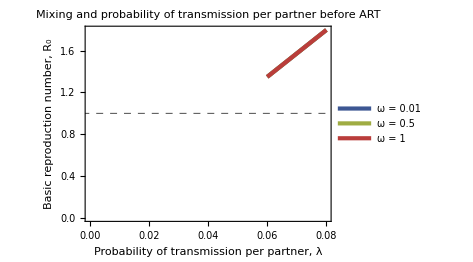

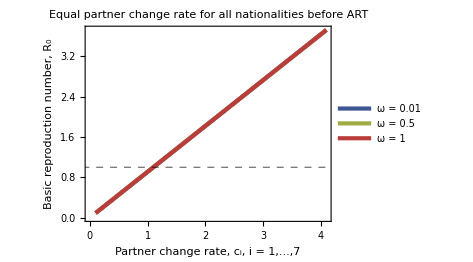

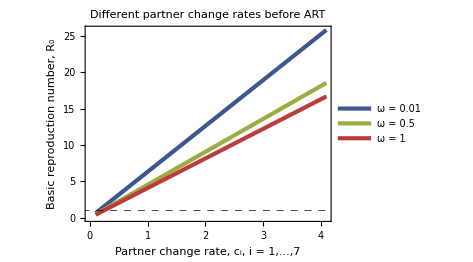

{{0.01,2.24756},{0.5,2.24756},{1,2.24756}}

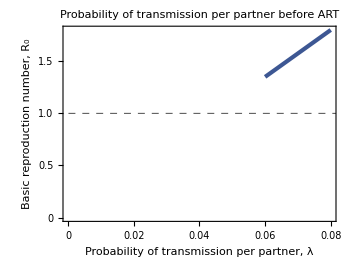

```mathematica
Print[Style["Jacobian before treatment",18,Orange,"Text"]]
JacobAnalytBT=Table[D[EqsList⟦All,2⟧[[k]],VarsList[[p]]],{k,NumLocations NumNationalities+1,2 NumLocations NumNationalities},{p,NumLocations NumNationalities+1,2 NumLocations NumNationalities}];

DiseaseFreeStateBT=Flatten[Join[Table[Subscript[T,i,j][t]->0,{i,Nationalities},{j,Locations}],Table[Subscript[IIf,i,j][t]->0,{i,Nationalities},{j,Locations}],Table[Subscript[Sf,i,j][t]->Subscript[NN0,i,j],{i,Nationalities},{j,Locations}]]];

JacobAnalytDiseaseFreeStateBT=JacobAnalytBT/.DiseaseFreeStateBT;

TransmissionMatrixBT=λ Table[Coefficient[JacobAnalytDiseaseFreeStateBT⟦k⟧⟦p⟧,λ],{k,1,NumLocations NumNationalities} ,{p,1,NumLocations NumNationalities}];
(*MatrixForm[TransmissionMatrixBT];*)
Dimensions[TransmissionMatrixBT];
TransitionMatrixBT=JacobAnalytDiseaseFreeStateBT-TransmissionMatrixBT;

NGMBT[migration_,year_,PercentInfected_,AverageRateA_,AverageRateB_,AverageRateC_,AverageRateNL_,AverageRateLA_,AverageRateOC_,AverageRateO_,PrevalenceNL_,PrevalenceLA_,PrevalenceOC_,PrevalenceO_,propTNL_,propTLA_,propTOC_,propTO_,propILA_,propILB_,propILC_,omega_,lambda_,tau_]:=-(TransmissionMatrixBT/.GeneralParameters[migration,year,PercentInfected,AverageRateA,AverageRateB,AverageRateC,AverageRateNL,AverageRateLA,AverageRateOC,AverageRateO,PrevalenceNL,PrevalenceLA,PrevalenceOC,PrevalenceO,propTNL,propTLA,propTOC,propTO,propILA,propILB,propILC,omega,lambda,tau]).Inverse[TransitionMatrixBT/.GeneralParameters[migration,year,PercentInfected,AverageRateA,AverageRateB,AverageRateC,AverageRateNL,AverageRateLA,AverageRateOC,AverageRateO,PrevalenceNL,PrevalenceLA,PrevalenceOC,PrevalenceO,propTNL,propTLA,propTOC,propTO,propILA,propILB,propILC,omega,lambda,tau]];

R0[migration_,year_,PercentInfected_,AverageRateA_,AverageRateB_,AverageRateC_,AverageRateNL_,AverageRateLA_,AverageRateOC_,AverageRateO_,PrevalenceNL_,PrevalenceLA_,PrevalenceOC_,PrevalenceO_,propTNL_,propTLA_,propTOC_,propTO_,propILA_,propILB_,propILC_,omega_,lambda_,tau_]:=Re[Eigenvalues[NGMBT[migration,year,PercentInfected,AverageRateA,AverageRateB,AverageRateC,AverageRateNL,AverageRateLA,AverageRateOC,AverageRateO,PrevalenceNL,PrevalenceLA,PrevalenceOC,PrevalenceO,propTNL,propTLA,propTOC,propTO,propILA,propILB,propILC,omega,lambda,tau]]⟦1⟧]

Print[Style["Basic reproduction number:",18,Orange,"Text"]]
R0["no",2020,0.01,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultPrevalenceNL,DefaultPrevalenceLA,DefaultPrevalenceOC,DefaultPrevalenceO,DefaultpropTNL,DefaultpropTLA,DefaultpropTOC,DefaultpropTO,DefaultILA,DefaultILB,DefaultILC,DefaultMixing,DefaultLambda,0]

MixingMin=0.01;
MixingMax=1;
MixingStep=0.5;

LambdaMin=0.06;
LambdaMax=0.08;
LambdaStep=0.01;

AverageRateMin=0.1;
AverageRateMax=4.1;
AverageRateStep=1;

(*MixingRange=Table[ω,{ω,MixingMin,MixingMax,MixingStep}];*)
MixingRange={0.01,0.5,1};
LambdaRange=Table[λ,{λ,LambdaMin,LambdaMax,LambdaStep}];
AverageRateRange=Table[cr,{cr,AverageRateMin,AverageRateMax,AverageRateStep}];

MixingLabels={"Assortative","Intermediate","Proportionate"};

AspRat=0.75;
ImSize=350;

PlotReproductionNumber[ReproductionNumberFunction_,migration_,year_,PercentInfected_,AverageRateA_,AverageRateB_,AverageRateC_,AverageRateNL_,AverageRateLA_,AverageRateOC_,AverageRateO_,PrevalenceNL_,PrevalenceLA_,PrevalenceOC_,PrevalenceO_,propTNL_,propTLA_,propTOC_,propTO_,propILA_,propILB_,propILC_,omega_,lambda_,tau_,par1_,par1Range_,par2_,par2Min_,par2Max_,xlabel_,ylabel_,ymax_,legendlabel_,plotlabel_]:=Plot[Evaluate@Table[ReproductionNumberFunction[migration,year,PercentInfected,AverageRateA,AverageRateB,AverageRateC,AverageRateNL,AverageRateLA,AverageRateOC,AverageRateO,PrevalenceNL,PrevalenceLA,PrevalenceOC,PrevalenceO,propTNL,propTLA,propTOC,propTO,propILA,propILB,propILC,omega,lambda,tau],{par1,par1Range}],{par2,par2Min,par2Max},AxesOrigin->{0,0},PlotRange->{{0,par2Max},{0,ymax}},Frame-> {{True,False},{True,False}},PlotRangePadding-> None,FrameStyle->Directive[Black,17],FrameLabel->{xlabel,ylabel},ImageSize->ImSize,PlotTheme->"Web",PlotStyle->ColorData["DarkRainbow"]/@Rescale[Range[Length[par1Range]]],GridLines->{None,{1}},GridLinesStyle->Directive[Black,Dashed,Thick],AspectRatio->AspRat,FrameTicksStyle->{{{Black,14,Opacity[1]},None},{{Black,14,Opacity[1]},None}},PlotLegends->Placed[Table[Style[Row[{legendlabel,par1}],Black,17],{par1,par1Range}](*{Scaled[{0.1,0.1}], {0.1, 0.1}}*),Right],PlotLabel->Style[ plotlabel(*Row[{"α=",ShapeParameterRange⟦i⟧,", σ^2=",VarianceContactRate[MeanRateData]/.α-> ShapeParameterRange⟦i⟧}]*),Black,17,Bold,"Text"]]

PlotReproductionNumberSimple[ReproductionNumberFunction_,migration_,year_,PercentInfected_,AverageRateA_,AverageRateB_,AverageRateC_,AverageRateNL_,AverageRateLA_,AverageRateOC_,AverageRateO_,PrevalenceNL_,PrevalenceLA_,PrevalenceOC_,PrevalenceO_,propTNL_,propTLA_,propTOC_,propTO_,propILA_,propILB_,propILC_,omega_,lambda_,tau_,par1_,par1Min_,par1Max_,xlabel_,ylabel_,ymax_,plotlabel_]:=Plot[Evaluate[ReproductionNumberFunction[migration,year,PercentInfected,AverageRateA,AverageRateB,AverageRateC,AverageRateNL,AverageRateLA,AverageRateOC,AverageRateO,PrevalenceNL,PrevalenceLA,PrevalenceOC,PrevalenceO,propTNL,propTLA,propTOC,propTO,propILA,propILB,propILC,omega,lambda,tau]],{par1,par1Min,par1Max},AxesOrigin->{0,0},PlotRange->{{0,par1Max},{0,ymax}},Frame-> {{True,False},{True,False}},PlotRangePadding-> None,FrameStyle->Directive[Black,17],FrameLabel->{xlabel,ylabel},ImageSize->ImSize,PlotTheme->"Web",PlotStyle->ColorData["DarkRainbow"]/@Rescale[Range[1]],GridLines->{None,{1}},GridLinesStyle->Directive[Black,Dashed,Thick],AspectRatio->AspRat,FrameTicksStyle->{{{Black,14,Opacity[1]},None},{{Black,14,Opacity[1]},None}},PlotLabel->Style[ plotlabel(*Row[{"α=",ShapeParameterRange⟦i⟧,", σ^2=",VarianceContactRate[MeanRateData]/.α-> ShapeParameterRange⟦i⟧}]*),Black,17,Bold,"Text"]]

PlotReproductionNumber[R0,"no",2020,0.01,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultPrevalenceNL,DefaultPrevalenceLA,DefaultPrevalenceOC,DefaultPrevalenceO,DefaultpropTNL,DefaultpropTLA,DefaultpropTOC,DefaultpropTO,DefaultILA,DefaultILB,DefaultILC,ω,λ,0,ω,MixingRange,λ,LambdaMin,LambdaMax,"Probability of transmission per partner, λ","Basic reproduction number, R_0",Automatic,"ω = ","Mixing and probability of\ntransmission per partner\nbefore ART"]

PlotReproductionNumber[R0,"no",2020,0.01,cr,cr,cr,cr,cr,cr,cr,DefaultPrevalenceNL,DefaultPrevalenceLA,DefaultPrevalenceOC,DefaultPrevalenceO,DefaultpropTNL,DefaultpropTLA,DefaultpropTOC,DefaultpropTO,DefaultILA,DefaultILB,DefaultILC,ω,DefaultLambda,0,ω,MixingRange,cr,AverageRateMin,AverageRateMax,"Partner change rate, c_i, i = 1,...,7","Basic reproduction number, R_0",Automatic,"ω = ","Equal partner change rate\nfor all nationalities\nbefore ART"]

PlotReproductionNumber[R0,"no",2020,0.01,cr,2 cr,3 cr,4 cr,5 cr,6 cr,7 cr,DefaultPrevalenceNL,DefaultPrevalenceLA,DefaultPrevalenceOC,DefaultPrevalenceO,DefaultpropTNL,DefaultpropTLA,DefaultpropTOC,DefaultpropTO,DefaultILA,DefaultILB,DefaultILC,ω,DefaultLambda,0,ω,MixingRange,cr,AverageRateMin,AverageRateMax,"Partner change rate, c_i, i = 1,...,7","Basic reproduction number, R_0",Automatic,"ω = ","Different partner change rates\nbefore ART"]

(*PlotReproductionNumberSimple[R0,"no",2020,0.01,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultPrevalenceNL,DefaultPrevalenceLA,DefaultPrevalenceOC,DefaultPrevalenceO,DefaultpropTNL,DefaultpropTLA,DefaultpropTOC,DefaultpropTO,DefaultILA,DefaultILB,DefaultILC,ω,DefaultLambda,0,ω,MixingMin,MixingMax,"Mixing, ω","Basic reproduction number, R_0","Mixing before ART"]*)

Table[{ω,R0["no",2020,0.01,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultPrevalenceNL,DefaultPrevalenceLA,DefaultPrevalenceOC,DefaultPrevalenceO,DefaultpropTNL,DefaultpropTLA,DefaultpropTOC,DefaultpropTO,DefaultILA,DefaultILB,DefaultILC,ω,DefaultLambda,0]},{ω,MixingRange}]

PlotReproductionNumberSimple[R0,"no",2020,0.01,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultPrevalenceNL,DefaultPrevalenceLA,DefaultPrevalenceOC,DefaultPrevalenceO,DefaultpropTNL,DefaultpropTLA,DefaultpropTOC,DefaultpropTO,DefaultILA,DefaultILB,DefaultILC,DefaultMixing,λ,0,λ,LambdaMin,LambdaMax,"Probability of transmission per partner, λ","Basic reproduction number, R_0",Automatic,"Probability of transmission per partner\nbefore ART"]
```

## Effective (R_e) reproduction number

Jacobian after treatment

Effective reproduction number:

1.12104

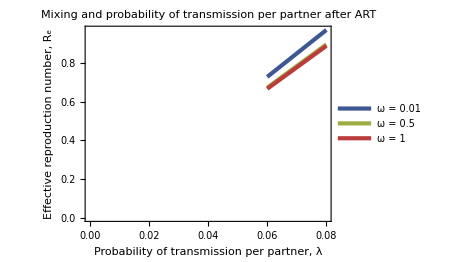

{{{0.,0.01,2.24756},{0.,0.5,2.24756},{0.,1,2.24756}},{{0.01,0.01,2.18721},{0.01,0.5,2.18236},{0.01,1,2.1823}},{{0.02,0.01,2.13646},{0.02,0.5,2.12214},{0.02,1,2.12191}},{{0.03,0.01,2.08947},{0.03,0.5,2.06637},{0.03,1,2.0659}},{{0.04,0.01,2.04564},{0.04,0.5,2.01461},{0.04,1,2.01385}},{{0.05,0.01,2.00452},{0.05,0.5,1.96647},{0.05,1,1.96539}},{{0.06,0.01,1.96588},{0.06,0.5,1.92163},{0.06,1,1.92021}},{{0.07,0.01,1.9295},{0.07,0.5,1.87978},{0.07,1,1.87801}},{{0.08,0.01,1.89521},{0.08,0.5,1.84069},{0.08,1,1.83856}},{{0.09,0.01,1.86288},{0.09,0.5,1.80411},{0.09,1,1.80164}},{{0.1,0.01,1.83238},{0.1,0.5,1.76986},{0.1,1,1.76705}},{{0.11,0.01,1.80359},{0.11,0.5,1.73776},{0.11,1,1.73462}},{{0.12,0.01,1.77642},{0.12,0.5,1.70766},{0.12,1,1.7042}},{{0.13,0.01,1.75076},{0.13,0.5,1.67941},{0.13,1,1.67565}},{{0.14,0.01,1.72654},{0.14,0.5,1.65291},{0.14,1,1.64886}},{{0.15,0.01,1.70368},{0.15,0.5,1.62803},{0.15,1,1.6237}},{{0.16,0.01,1.68212},{0.16,0.5,1.60468},{0.16,1,1.60009}},{{0.17,0.01,1.66178},{0.17,0.5,1.58277},{0.17,1,1.57794}},{{0.18,0.01,1.64263},{0.18,0.5,1.56222},{0.18,1,1.55717}},{{0.19,0.01,1.62461},{0.19,0.5,1.54296},{0.19,1,1.5377}},{{0.2,0.01,1.60766},{0.2,0.5,1.52494},{0.2,1,1.51948}}}

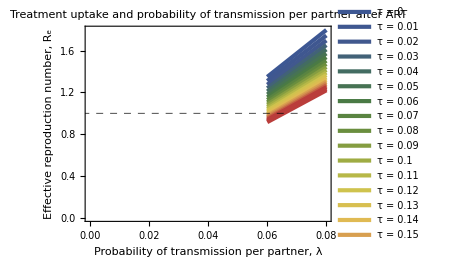

((0.
0.06
1.34854) | (0.
0.07
1.57329) | (0.
0.08
1.79805)
(0.01
0.06
1.30942) | (0.01
0.07
1.52765) | (0.01
0.08
1.74589)
(0.02
0.06
1.27328) | (0.02
0.07
1.4855) | (0.02
0.08
1.69771)
(0.03
0.06
1.23982) | (0.03
0.07
1.44646) | (0.03
0.08
1.65309)
(0.04
0.06
1.20876) | (0.04
0.07
1.41022) | (0.04
0.08
1.61169)
(0.05
0.06
1.17988) | (0.05
0.07
1.37653) | (0.05
0.08
1.57318)
(0.06
0.06
1.14455) | (0.06
0.07
1.34514) | (0.06
0.08
1.5373)
(0.07
0.06
1.12787) | (0.07
0.07
1.30302) | (0.07
0.08
1.50383)
(0.08
0.06
1.10441) | (0.08
0.07
1.28848) | (0.08
0.08
1.45416)
(0.09
0.06
1.08247) | (0.09
0.07
1.26288) | (0.09
0.08
1.44329)
(0.1
0.06
1.06192) | (0.1
0.07
1.2389) | (0.1
0.08
1.41589)
(0.11
0.06
1.04266) | (0.11
0.07
1.21643) | (0.11
0.08
1.39021)
(0.12
0.06
1.0246) | (0.12
0.07
1.19536) | (0.12
0.08
1.36613)
(0.13
0.06
1.00765) | (0.13
0.07
1.17559) | (0.13
0.08
1.34353)
(0.14
0.06
0.991745) | (0.14
0.07
1.15704) | (0.14
0.08
1.32233)
(0.15
0.06
0.976817) | (0.15
0.07
1.13962) | (0.15
0.08
1.30242)
(0.16
0.06
0.962806) | (0.16
0.07
1.12327) | (0.16
0.08
1.28374)
(0.17
0.06
0.94966) | (0.17
0.07
1.10794) | (0.17
0.08
1.26621)
(0.18
0.06
0.937331) | (0.18
0.07
1.09355) | (0.18
0.08
1.24978)
(0.19
0.06
0.925779) | (0.19
0.07
1.08008) | (0.19
0.08
1.23437)
(0.2
0.06
0.914964) | (0.2
0.07
1.06746) | (0.2
0.08
1.21995))

```mathematica
Print[Style["Jacobian after treatment",18,Orange,"Text"]]
JacobAnalytAT=Table[D[EqsList⟦All,2⟧[[k]],VarsList[[p]]],{k,NumLocations NumNationalities+1,3 NumLocations NumNationalities},{p,NumLocations NumNationalities+1,3 NumLocations NumNationalities}];

DiseaseFreeStateAT=Flatten[Join[Table[Subscript[T,i,j][t]->0,{i,Nationalities},{j,Locations}],Table[Subscript[IIf,i,j][t]->0,{i,Nationalities},{j,Locations}],Table[Subscript[Sf,i,j][t]->Subscript[NN0,i,j],{i,Nationalities},{j,Locations}]]];

JacobAnalytDiseaseFreeStateAT=JacobAnalytAT/.DiseaseFreeStateAT;

TransmissionMatrixAT=λ Table[Coefficient[JacobAnalytDiseaseFreeStateAT⟦k⟧⟦p⟧,λ],{k,1,2 NumLocations NumNationalities} ,{p,1,2 NumLocations NumNationalities}];
(*MatrixForm[TransmissionMatrixBT];*)
Dimensions[TransmissionMatrixAT];
TransitionMatrixAT=JacobAnalytDiseaseFreeStateAT-TransmissionMatrixAT;

NGMAT[migration_,year_,PercentInfected_,AverageRateA_,AverageRateB_,AverageRateC_,AverageRateNL_,AverageRateLA_,AverageRateOC_,AverageRateO_,PrevalenceNL_,PrevalenceLA_,PrevalenceOC_,PrevalenceO_,propTNL_,propTLA_,propTOC_,propTO_,propILA_,propILB_,propILC_,omega_,lambda_,tau_]:=-(TransmissionMatrixAT/.GeneralParameters[migration,year,PercentInfected,AverageRateA,AverageRateB,AverageRateC,AverageRateNL,AverageRateLA,AverageRateOC,AverageRateO,PrevalenceNL,PrevalenceLA,PrevalenceOC,PrevalenceO,propTNL,propTLA,propTOC,propTO,propILA,propILB,propILC,omega,lambda,tau]).Inverse[TransitionMatrixAT/.GeneralParameters[migration,year,PercentInfected,AverageRateA,AverageRateB,AverageRateC,AverageRateNL,AverageRateLA,AverageRateOC,AverageRateO,PrevalenceNL,PrevalenceLA,PrevalenceOC,PrevalenceO,propTNL,propTLA,propTOC,propTO,propILA,propILB,propILC,omega,lambda,tau]];

Reff[migration_,year_,PercentInfected_,AverageRateA_,AverageRateB_,AverageRateC_,AverageRateNL_,AverageRateLA_,AverageRateOC_,AverageRateO_,PrevalenceNL_,PrevalenceLA_,PrevalenceOC_,PrevalenceO_,propTNL_,propTLA_,propTOC_,propTO_,propILA_,propILB_,propILC_,omega_,lambda_,tau_]:=Re[Eigenvalues[NGMAT[migration,year,PercentInfected,AverageRateA,AverageRateB,AverageRateC,AverageRateNL,AverageRateLA,AverageRateOC,AverageRateO,PrevalenceNL,PrevalenceLA,PrevalenceOC,PrevalenceO,propTNL,propTLA,propTOC,propTO,propILA,propILB,propILC,omega,lambda,tau]]⟦1⟧]

Print[Style["Effective reproduction number:",18,Orange,"Text"]]
Reff["no",2020,0.01,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultPrevalenceNL,DefaultPrevalenceLA,DefaultPrevalenceOC,DefaultPrevalenceO,DefaultpropTNL,DefaultpropTLA,DefaultpropTOC,DefaultpropTO,DefaultILA,DefaultILB,DefaultILC,DefaultMixing,DefaultLambda,DefaultTreatmentUptake]

TreatmentUptakeMin=0;
TreatmentUptakeMax=0.2;
TreatmentUptakeStep=0.01;

TreatmentUptakeRange=Table[τ,{τ,TreatmentUptakeMin,TreatmentUptakeMax,TreatmentUptakeStep}];

PlotReproductionNumber[Reff,"no",2020,0.01,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultPrevalenceNL,DefaultPrevalenceLA,DefaultPrevalenceOC,DefaultPrevalenceO,DefaultpropTNL,DefaultpropTLA,DefaultpropTOC,DefaultpropTO,DefaultILA,DefaultILB,DefaultILC,ω,λ,DefaultTreatmentUptake,ω,MixingRange,λ,LambdaMin,LambdaMax,"Probability of transmission per partner, λ","Effective reproduction number, R_e",Automatic,"ω = ","Mixing and probability of\ntransmission per partner\nafter ART"]

Table[{τ,ω,Reff["no",2020,0.01,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultPrevalenceNL,DefaultPrevalenceLA,DefaultPrevalenceOC,DefaultPrevalenceO,DefaultpropTNL,DefaultpropTLA,DefaultpropTOC,DefaultpropTO,DefaultILA,DefaultILB,DefaultILC,ω,DefaultLambda,τ]},{τ,TreatmentUptakeRange},{ω,MixingRange}]

PlotReproductionNumber[Reff,"no",2020,0.01,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultPrevalenceNL,DefaultPrevalenceLA,DefaultPrevalenceOC,DefaultPrevalenceO,DefaultpropTNL,DefaultpropTLA,DefaultpropTOC,DefaultpropTO,DefaultILA,DefaultILB,DefaultILC,DefaultMixing,λ,τ,τ,TreatmentUptakeRange,λ,LambdaMin,LambdaMax,"Probability of transmission per partner, λ","Effective reproduction number, R_e",Automatic,"τ = ","Treatment uptake and probability of\ntransmission per partner\nafter ART"]

Table[{τ,λ,Reff["no",2020,0.01,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultPrevalenceNL,DefaultPrevalenceLA,DefaultPrevalenceOC,DefaultPrevalenceO,DefaultpropTNL,DefaultpropTLA,DefaultpropTOC,DefaultpropTO,DefaultILA,DefaultILB,DefaultILC,DefaultMixing,λ,τ]},{τ,TreatmentUptakeRange},{λ,LambdaRange}]//MatrixForm
```

## Solving equations

```mathematica
Print[Style["Start time (full model)",18,Orange,"Text"]]
Subscript[t, start]=0
Print[Style["End time (full model)",18,Orange,"Text"]]
Subscript[t, end]=5

Subscript[t, endsteady]=200

Print[Style["Initial conditions (full model)",18,Orange,"Text"]]
ICs={Table[icSf[i,j]=Subscript[Sf0,i,j]==Subscript[Sf,i,j][t]/.{t->Subscript[t, start]},{i,Nationalities},{j,Locations}],Table[icIf[i,j]=Subscript[IIf0,i,j]==Subscript[IIf,i,j][t]/.{t->Subscript[t, start]},{i,Nationalities},{j,Locations}],Table[icT[i,j]=Subscript[T0,i,j]==Subscript[T,i,j][t]/.{t->Subscript[t, start]},{i,Nationalities},{j,Locations}],Table[icA[i,j]=Subscript[A0,i,j]==Subscript[A,i,j][t]/.{t->Subscript[t, start]},{i,Nationalities},{j,Locations}],Table[icNNf[i,j]=Subscript[NNf0,i,j]==Subscript[NNf,i,j][t]/.{t->Subscript[t, start]},{i,Nationalities},{j,InteractingRegions}]}

Print[Style["Initial conditions list (full model)",18,Orange,"Text"]]
ICsList=Flatten[ICs];

Print[Style["Length of initial conditions list (full model)",18,Orange,"Text"]]
Length[ICsList]

solution2015MigrationZeroInfection=NDSolve[Join[EqsList,ICsList]/.Parameters2015MigrationZeroInfection,VarsList,{t,Subscript[t, start],Subscript[t, end]}(*, Method->"StiffnessSwitching"*)];

solution2020NoMigrationInfection=NDSolve[Join[EqsList,ICsList]/.Parameters2020NoMigrationInfection,VarsList,{t,Subscript[t, start],Subscript[t, endsteady]}(*, Method->"StiffnessSwitching"*)];
```

Start time (full model)

0

End time (full model)

5

200

Initial conditions (full model)

{{{Sf0_(1,1)==Sf_(1,1)[0],Sf0_(1,2)==Sf_(1,2)[0],Sf0_(1,3)==Sf_(1,3)[0]},{Sf0_(2,1)==Sf_(2,1)[0],Sf0_(2,2)==Sf_(2,2)[0],Sf0_(2,3)==Sf_(2,3)[0]},{Sf0_(3,1)==Sf_(3,1)[0],Sf0_(3,2)==Sf_(3,2)[0],Sf0_(3,3)==Sf_(3,3)[0]},{Sf0_(4,1)==Sf_(4,1)[0],Sf0_(4,2)==Sf_(4,2)[0],Sf0_(4,3)==Sf_(4,3)[0]},{Sf0_(5,1)==Sf_(5,1)[0],Sf0_(5,2)==Sf_(5,2)[0],Sf0_(5,3)==Sf_(5,3)[0]},{Sf0_(6,1)==Sf_(6,1)[0],Sf0_(6,2)==Sf_(6,2)[0],Sf0_(6,3)==Sf_(6,3)[0]},{Sf0_(7,1)==Sf_(7,1)[0],Sf0_(7,2)==Sf_(7,2)[0],Sf0_(7,3)==Sf_(7,3)[0]}},{{IIf0_(1,1)==IIf_(1,1)[0],IIf0_(1,2)==IIf_(1,2)[0],IIf0_(1,3)==IIf_(1,3)[0]},{IIf0_(2,1)==IIf_(2,1)[0],IIf0_(2,2)==IIf_(2,2)[0],IIf0_(2,3)==IIf_(2,3)[0]},{IIf0_(3,1)==IIf_(3,1)[0],IIf0_(3,2)==IIf_(3,2)[0],IIf0_(3,3)==IIf_(3,3)[0]},{IIf0_(4,1)==IIf_(4,1)[0],IIf0_(4,2)==IIf_(4,2)[0],IIf0_(4,3)==IIf_(4,3)[0]},{IIf0_(5,1)==IIf_(5,1)[0],IIf0_(5,2)==IIf_(5,2)[0],IIf0_(5,3)==IIf_(5,3)[0]},{IIf0_(6,1)==IIf_(6,1)[0],IIf0_(6,2)==IIf_(6,2)[0],IIf0_(6,3)==IIf_(6,3)[0]},{IIf0_(7,1)==IIf_(7,1)[0],IIf0_(7,2)==IIf_(7,2)[0],IIf0_(7,3)==IIf_(7,3)[0]}},{{T0_(1,1)==T_(1,1)[0],T0_(1,2)==T_(1,2)[0],T0_(1,3)==T_(1,3)[0]},{T0_(2,1)==T_(2,1)[0],T0_(2,2)==T_(2,2)[0],T0_(2,3)==T_(2,3)[0]},{T0_(3,1)==T_(3,1)[0],T0_(3,2)==T_(3,2)[0],T0_(3,3)==T_(3,3)[0]},{T0_(4,1)==T_(4,1)[0],T0_(4,2)==T_(4,2)[0],T0_(4,3)==T_(4,3)[0]},{T0_(5,1)==T_(5,1)[0],T0_(5,2)==T_(5,2)[0],T0_(5,3)==T_(5,3)[0]},{T0_(6,1)==T_(6,1)[0],T0_(6,2)==T_(6,2)[0],T0_(6,3)==T_(6,3)[0]},{T0_(7,1)==T_(7,1)[0],T0_(7,2)==T_(7,2)[0],T0_(7,3)==T_(7,3)[0]}},{{A0_(1,1)==A_(1,1)[0],A0_(1,2)==A_(1,2)[0],A0_(1,3)==A_(1,3)[0]},{A0_(2,1)==A_(2,1)[0],A0_(2,2)==A_(2,2)[0],A0_(2,3)==A_(2,3)[0]},{A0_(3,1)==A_(3,1)[0],A0_(3,2)==A_(3,2)[0],A0_(3,3)==A_(3,3)[0]},{A0_(4,1)==A_(4,1)[0],A0_(4,2)==A_(4,2)[0],A0_(4,3)==A_(4,3)[0]},{A0_(5,1)==A_(5,1)[0],A0_(5,2)==A_(5,2)[0],A0_(5,3)==A_(5,3)[0]},{A0_(6,1)==A_(6,1)[0],A0_(6,2)==A_(6,2)[0],A0_(6,3)==A_(6,3)[0]},{A0_(7,1)==A_(7,1)[0],A0_(7,2)==A_(7,2)[0],A0_(7,3)==A_(7,3)[0]}},{{NNf0_(1,4)==NNf_(1,4)[0],NNf0_(1,5)==NNf_(1,5)[0],NNf0_(1,6)==NNf_(1,6)[0],NNf0_(1,7)==NNf_(1,7)[0]},{NNf0_(2,4)==NNf_(2,4)[0],NNf0_(2,5)==NNf_(2,5)[0],NNf0_(2,6)==NNf_(2,6)[0],NNf0_(2,7)==NNf_(2,7)[0]},{NNf0_(3,4)==NNf_(3,4)[0],NNf0_(3,5)==NNf_(3,5)[0],NNf0_(3,6)==NNf_(3,6)[0],NNf0_(3,7)==NNf_(3,7)[0]},{NNf0_(4,4)==NNf_(4,4)[0],NNf0_(4,5)==NNf_(4,5)[0],NNf0_(4,6)==NNf_(4,6)[0],NNf0_(4,7)==NNf_(4,7)[0]},{NNf0_(5,4)==NNf_(5,4)[0],NNf0_(5,5)==NNf_(5,5)[0],NNf0_(5,6)==NNf_(5,6)[0],NNf0_(5,7)==NNf_(5,7)[0]},{NNf0_(6,4)==NNf_(6,4)[0],NNf0_(6,5)==NNf_(6,5)[0],NNf0_(6,6)==NNf_(6,6)[0],NNf0_(6,7)==NNf_(6,7)[0]},{NNf0_(7,4)==NNf_(7,4)[0],NNf0_(7,5)==NNf_(7,5)[0],NNf0_(7,6)==NNf_(7,6)[0],NNf0_(7,7)==NNf_(7,7)[0]}}}

Initial conditions list (full model)

Length of initial conditions list (full model)

112

## Steady states

```mathematica
solutionAT=Table[NDSolve[Join[EqsList,ICsList]/.GeneralParameters["no",2020,0.01,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultPrevalenceNL,DefaultPrevalenceLA,DefaultPrevalenceOC,DefaultPrevalenceO,DefaultpropTNL,DefaultpropTLA,DefaultpropTOC,DefaultpropTO,DefaultILA,DefaultILB,DefaultILC,DefaultMixing,λ,τ],VarsList,{t,Subscript[t, start],Subscript[t, endsteady]}(*, Method->"StiffnessSwitching"*)],{τ,TreatmentUptakeRange},{λ,LambdaRange}];
```

## Plot steady states

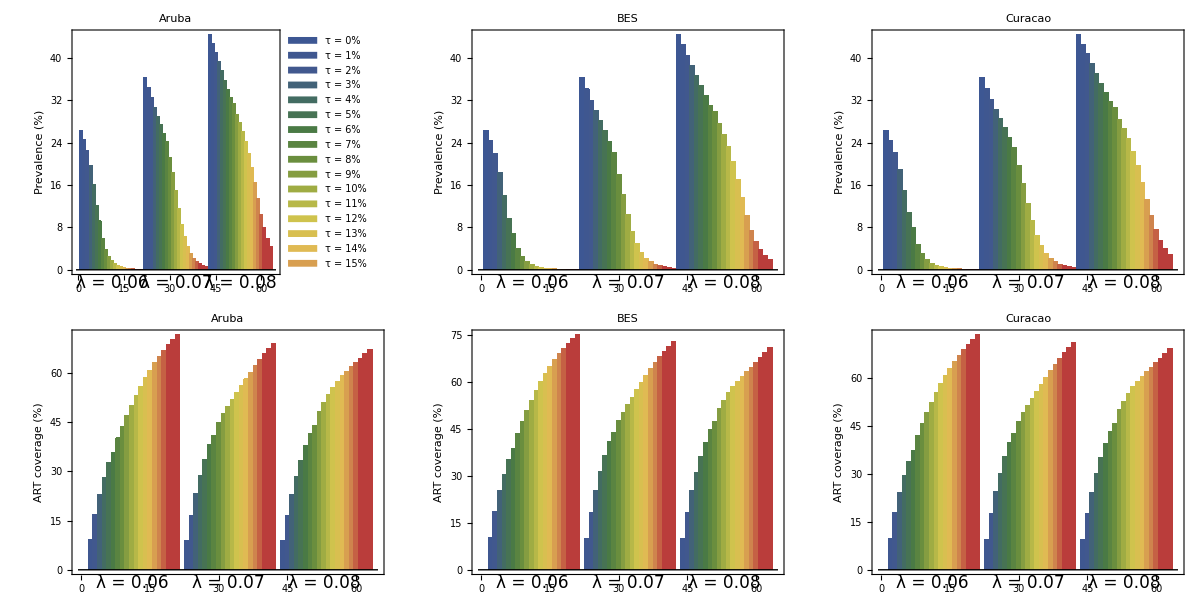

```mathematica
PlotPrev[var_,plotlabel_,ylabel_]:=BarChart[Table[Flatten[Table[Flatten[(100 var/.t-> Subscript[t, endsteady])/.(solutionAT/.t-> Subscript[t, endsteady])⟦τ,λ⟧],{τ,1,Length[TreatmentUptakeRange]}]],{λ,1,Length[LambdaRange]}],AspectRatio->AspRat,ImageSize->ImSize,PlotRangePadding->None,ChartBaseStyle->EdgeForm[None],ChartStyle->ColorData["DarkRainbow"]/@Rescale[Range[Length[TreatmentUptakeRange]]],ChartLabels->{Placed[Table[Style[Row[{(*MixLab⟦mixing⟧,*)"λ = ",LambdaRange⟦λ⟧}],Black,17],{λ,1,Length[LambdaRange]}],Below],None},Frame-> Left,FrameStyle->Directive[Black,17],FrameLabel-> {{ylabel,None},{None,None}},ChartLayout->"Grouped",(*ChartLegends->Placed[Table[Style[Row[{"τ = ",Round[τ],"%"}],Black,17],{τ,100 TreatmentUptakeRange}],Below],*)PlotLabel->Style[Row[{plotlabel}],Black,17,Bold,"Text"]]

Legended[Grid[{{PlotPrev[PrevAruba,"Aruba","Prevalence (%)"],PlotPrev[PrevBES,"BES","Prevalence (%)"],PlotPrev[PrevCuracao,"Curacao","Prevalence (%)"]},{PlotPrev[ARTCoverageAruba,"Aruba","ART coverage (%)"],PlotPrev[ARTCoverageBES,"BES","ART coverage (%)"],PlotPrev[ARTCoverageCuracao,"Curacao","ART coverage (%)"]}}],Placed[SwatchLegend[ColorData["DarkRainbow"]/@Rescale[Range[Length[TreatmentUptakeRange]]],Table[Style[Row[{"τ = ",Round[τ],"%"}],Black,17],{τ,100 TreatmentUptakeRange}]],After]]
```

## Baseline

```mathematica
BaselineLambda=0.07;
BaselineTreatmentUptake=0.15;

solutionBaseline[BaselineLambda_,BaselineTreatmentUptake_,DefaultILA_,DefaultILB_,DefaultILC_]:=NDSolve[Join[EqsList,ICsList]/.GeneralParameters["no",2020,0.01,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultPrevalenceNL,DefaultPrevalenceLA,DefaultPrevalenceOC,DefaultPrevalenceO,DefaultpropTNL,DefaultpropTLA,DefaultpropTOC,DefaultpropTO,DefaultILA,DefaultILB,DefaultILC,DefaultMixing,BaselineLambda,BaselineTreatmentUptake],VarsList,{t,Subscript[t, start],Subscript[t, endsteady]}(*, Method->"StiffnessSwitching"*)];

PrintHIVPrevARTCoverage[VarPrev_,VarARTCoverage_,BaselineLambda_,BaselineTreatmentUptake_,DefaultILA_,DefaultILB_,DefaultILC_]:={(100 VarPrev/.t-> Subscript[t, endsteady])/.(solutionBaseline[BaselineLambda,BaselineTreatmentUptake,DefaultILA,DefaultILB,DefaultILC]/.t-> Subscript[t, endsteady])⟦1⟧,(100 VarARTCoverage/.t-> Subscript[t, endsteady])/.(solutionBaseline[BaselineLambda,BaselineTreatmentUptake,DefaultILA,DefaultILB,DefaultILC]/.t-> Subscript[t, endsteady])⟦1⟧,Reff["no",2020,0.01,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultPrevalenceNL,DefaultPrevalenceLA,DefaultPrevalenceOC,DefaultPrevalenceO,DefaultpropTNL,DefaultpropTLA,DefaultpropTOC,DefaultpropTO,DefaultILA,DefaultILB,DefaultILC,DefaultMixing,BaselineLambda,BaselineTreatmentUptake]};

Print["Baseline HIV prevalence and ART coverage"];
PrintHIVPrevARTCoverage[PrevAruba,ARTCoverageAruba,BaselineLambda,BaselineTreatmentUptake,DefaultILA,DefaultILB,DefaultILC]
PrintHIVPrevARTCoverage[PrevBES,ARTCoverageBES,BaselineLambda,BaselineTreatmentUptake,DefaultILA,DefaultILB,DefaultILC]
PrintHIVPrevARTCoverage[PrevCuracao,ARTCoverageCuracao,BaselineLambda,BaselineTreatmentUptake,DefaultILA,DefaultILB,DefaultILC]

Print["Increased testing and ART uptake: prevalence and ART coverage"];
PrintHIVPrevARTCoverage[PrevAruba,ARTCoverageAruba,BaselineLambda,BaselineTreatmentUptake 1.25,DefaultILA,DefaultILB,DefaultILC]
PrintHIVPrevARTCoverage[PrevBES,ARTCoverageBES,BaselineLambda,BaselineTreatmentUptake 1.25,DefaultILA,DefaultILB,DefaultILC]
PrintHIVPrevARTCoverage[PrevCuracao,ARTCoverageCuracao,BaselineLambda,BaselineTreatmentUptake 1.25,DefaultILA,DefaultILB,DefaultILC]

Print["Illegal migrants: prevalence and ART coverage"];
PrintHIVPrevARTCoverage[PrevAruba,ARTCoverageAruba,BaselineLambda,BaselineTreatmentUptake,0,DefaultILB,DefaultILC]
PrintHIVPrevARTCoverage[PrevBES,ARTCoverageBES,BaselineLambda,BaselineTreatmentUptake,DefaultILA,0,DefaultILC]
PrintHIVPrevARTCoverage[PrevCuracao,ARTCoverageCuracao,BaselineLambda,BaselineTreatmentUptake,DefaultILA,DefaultILB,0]


(*Table[{i,BaselineTreatmentUptake i,Reff["no",2020,0.01,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultAverageRate,DefaultPrevalenceNL,DefaultPrevalenceLA,DefaultPrevalenceOC,DefaultPrevalenceO,DefaultpropTNL,DefaultpropTLA,DefaultpropTOC,DefaultpropTO,DefaultILA,DefaultILB,DefaultILC,DefaultMixing,BaselineLambda,BaselineTreatmentUptake i]},{i,1,2,0.05}]*)
```

Baseline HIV prevalence and ART coverage

{3.08382,60.2237,1.06867}

{1.50596,64.2362,1.06867}

{2.1366,62.2868,1.06867}

Increased testing and ART uptake: prevalence and ART coverage

{0.882285,67.1381,0.984275}

{0.421791,71.1202,0.984275}

{0.601356,69.2098,0.984275}

Illegal migrants: prevalence and ART coverage

{1.19074,65.5265,1.04382}

{1.19074,65.5265,1.06867}

{1.19074,65.5265,1.06867}

## Plotting solutions

Full model plots

Plot number of individuals

Parameters: 2015 + migration + zero infection

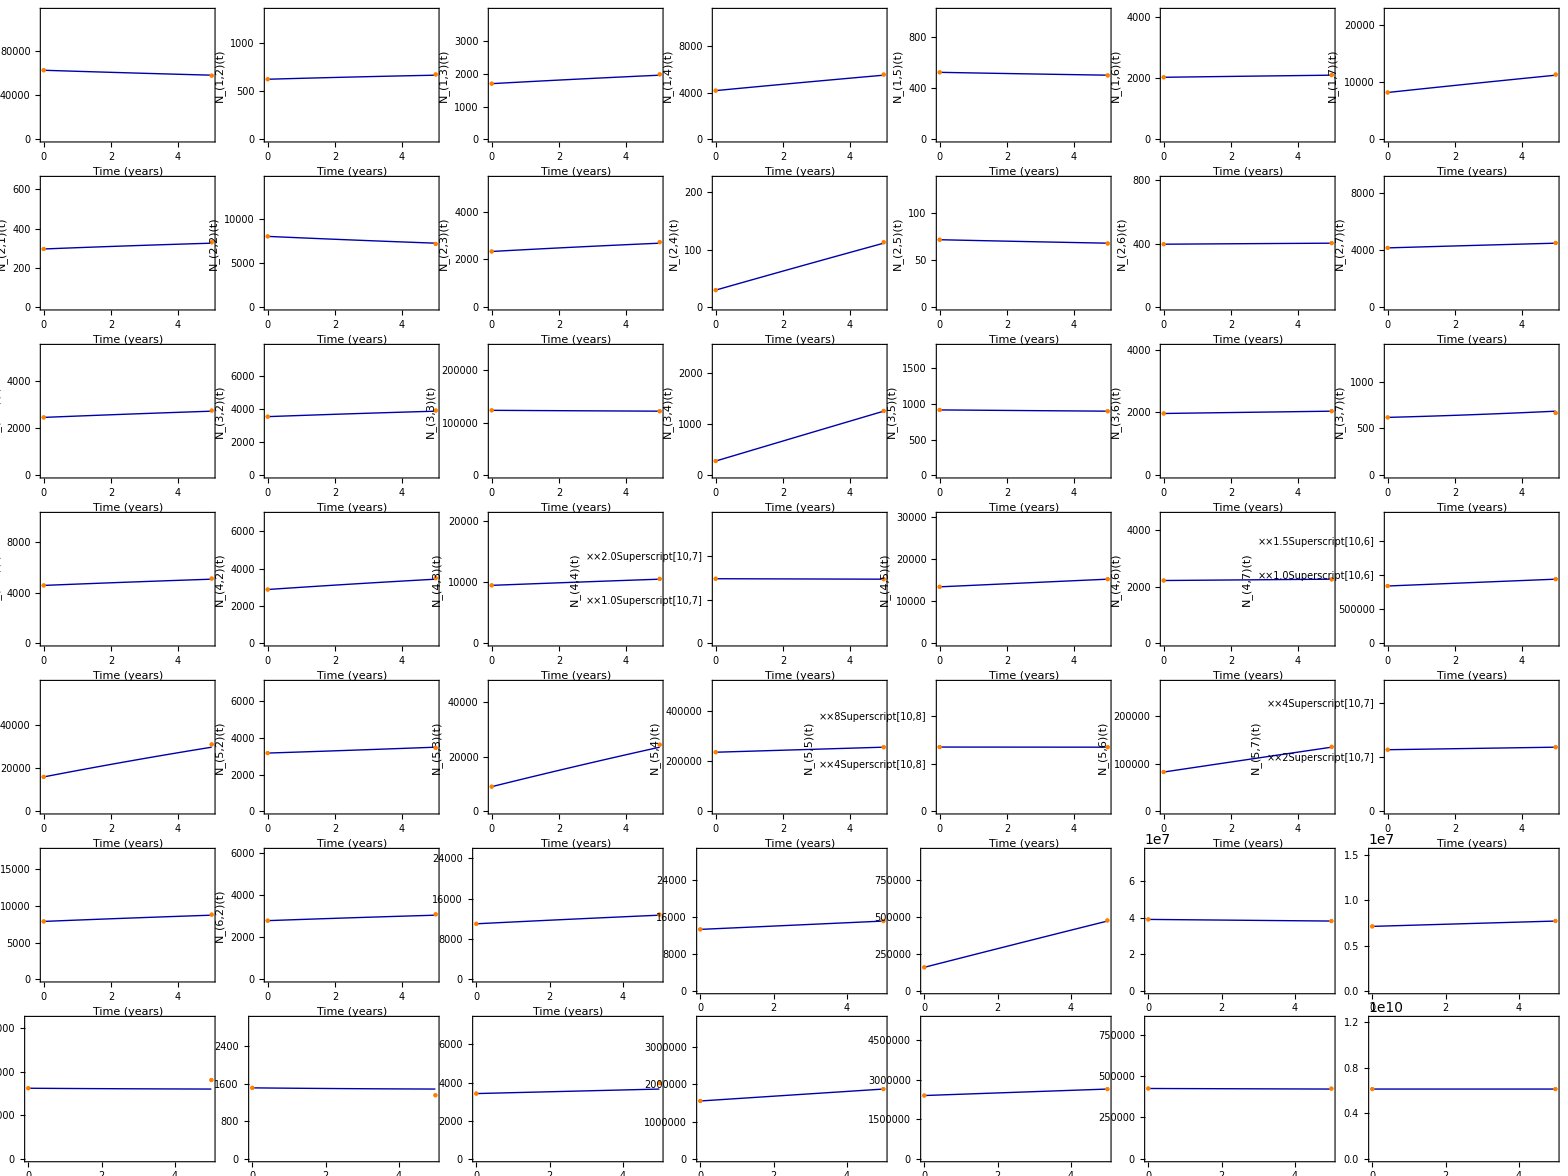

```mathematica
Print[Style["Full model plots",18,Orange,"Text"]]
Print[Style["Plot number of individuals",18,Orange,"Text"]]


PlotSolution[solution_,tstart_,tend_,data1_,data2_]:=Grid[Table[Show[Plot[Evaluate[Subscript[NNf,i,j][t]/.solution],{t,Subscript[t, start],Subscript[t, end]},AspectRatio->0.75,ImageSize->250,PlotRangePadding->{{0.1,0.15},{0,Automatic}},PlotRange->{{0,Subscript[t, end]},{0,2 ((Subscript[NNf,i,j][t]/.solution)/.t-> Subscript[t, end])⟦1⟧}},PlotStyle->{Thick,Darker[Blue]},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},Ticks->{Automatic,Automatic},PlotTheme-> "Web",FrameStyle->Directive[Black,17],ImagePadding->{{100,Automatic},{Automatic,Automatic}},(*PlotLabel->Style[Row[{intList⟦it⟧}],Black,17],*)FrameLabel-> {{Subscript[N, i,j][t],None},{"Time (years)",None}}],ListPlot[{{tstart,data1[[i,j]]}},PlotStyle->Directive[PointSize[Large],Orange]],ListPlot[{{tend,data2[[i,j]]}},PlotStyle->Directive[PointSize[Large],Orange]]],{i,Nationalities},{j,Nationalities}]]

Print[Style["Parameters: 2015 + migration + zero infection",18,Orange,"Text"]]
PlotSolution[solution2015MigrationZeroInfection,Subscript[t, start],Subscript[t, end],DemographyMatrix2015,DemographyMatrix2020]
```

## Sanity checks

```mathematica
Print[Style["Infected, treated and deceased at t=tstart in ABC",18,Orange,"Text"]]
Table[{((Subscript[IIf,i,j][t]/.solution2015MigrationZeroInfection)/.t-> Subscript[t, start])⟦1⟧,((Subscript[T,i,j][t]/.solution2015MigrationZeroInfection)/.t-> Subscript[t, start])⟦1⟧,((Subscript[A,i,j][t]/.solution2015MigrationZeroInfection)/.t-> Subscript[t, start])⟦1⟧},{i,Nationalities},{j,Locations}]

Print[Style["Infected, treated and deceased at t=tend in ABC",18,Orange,"Text"]]
Table[{((Subscript[IIf,i,j][t]/.solution2015MigrationZeroInfection)/.t-> Subscript[t, end])⟦1⟧,((Subscript[T,i,j][t]/.solution2015MigrationZeroInfection)/.t-> Subscript[t, end])⟦1⟧,((Subscript[A,i,j][t]/.solution2015MigrationZeroInfection)/.t-> Subscript[t, end])⟦1⟧},{i,Nationalities},{j,Locations}]

Print[Style["Susceptible equal to total population at t=tstart in ABC",18,Orange,"Text"]]
Table[{((Subscript[Sf,i,j][t]/.solution2015MigrationZeroInfection)/.t-> Subscript[t, start])⟦1⟧,((Subscript[NNf,i,j][t]/.solution2015MigrationZeroInfection)/.t->  Subscript[t, start])⟦1⟧},{i,Nationalities},{j,Locations}]

Print[Style["Susceptible equal to total population at t=tend in ABC",18,Orange,"Text"]]
Table[{((Subscript[Sf,i,j][t]/.solution2015MigrationZeroInfection)/.t-> Subscript[t, end])⟦1⟧,((Subscript[NNf,i,j][t]/.solution2015MigrationZeroInfection)/.t-> Subscript[t, end])⟦1⟧},{i,Nationalities},{j,Locations}]

Print[Style["Initial population at t=tstart in ABC + interacting regions and 2015 population data",18,Orange,"Text"]]
Table[{((Subscript[NNf,i,j][t]/.solution2015MigrationZeroInfection)/.t-> Subscript[t, start])⟦1⟧,DemographyMatrix2015⟦i,j⟧,((Subscript[NNf,i,j][t]/.solution2015MigrationZeroInfection)/.t-> Subscript[t, start])⟦1⟧-DemographyMatrix2015⟦i,j⟧},{i,Nationalities},{j,Nationalities}]

Print[Style["Initial population at t=tend in ABC + interacting regions and 2020 population data",18,Orange,"Text"]]
Table[{((Subscript[NNf,i,j][t]/.solution2015MigrationZeroInfection)/.t-> Subscript[t, end])⟦1⟧,DemographyMatrix2020⟦i,j⟧,i,j,(((Subscript[NNf,i,j][t]/.solution2015MigrationZeroInfection)/.t-> Subscript[t, end])⟦1⟧-DemographyMatrix2020⟦i,j⟧)/((Subscript[NNf,i,j][t]/.solution2015MigrationZeroInfection)/.t-> Subscript[t, end])⟦1⟧},{i,Nationalities},{j,Nationalities}]//MatrixForm
```

Infected, treated and deceased at t=tstart in ABC

{{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}},{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}},{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}},{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}},{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}},{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}},{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}}}

Infected, treated and deceased at t=tend in ABC

{{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}},{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}},{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}},{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}},{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}},{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}},{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}}}

Susceptible equal to total population at t=tstart in ABC

{{{62815.,62815.},{625.,625.},{1708.,1708.}},{{297.,297.},{8038.,8038.},{2334.,2334.}},{{2455.,2455.},{3540.,3540.},{123820.,123820.}},{{4585.,4585.},{2880.,2880.},{9504.,9504.}},{{16028.,16028.},{3175.,3175.},{9052.,9052.}},{{7884.,7884.},{2797.,2797.},{11027.,11027.}},{{3247.,3247.},{1510.,1510.},{3422.,3422.}}}

Susceptible equal to total population at t=tend in ABC

{{{58340.5,58340.5},{667.295,667.295},{1967.6,1967.6}},{{326.519,326.519},{7268.88,7268.88},{2680.31,2680.31}},{{2718.74,2718.74},{3868.71,3868.71},{122185.,122185.}},{{5078.29,5078.29},{3432.17,3432.17},{10514.8,10514.8}},{{29857.9,29857.9},{3495.49,3495.49},{23521.,23521.}},{{8733.87,8733.87},{3057.19,3057.19},{12734.3,12734.3}},{{3209.38,3209.38},{1484.44,1484.44},{3657.84,3657.84}}}

Initial population at t=tstart in ABC + interacting regions and 2015 population data

{{{62815.,62815,0.},{625.,625,0.},{1708.,1708,0.},{4178.,4178,0.},{522.,522,0.},{2028.,2028,0.},{8185.,8185,0.}},{{297.,297,0.},{8038.,8038,0.},{2334.,2334,0.},{30.,30,0.},{72.,72,0.},{396.,396,0.},{4166.,4166,0.}},{{2455.,2455,0.},{3540.,3540,0.},{123820.,123820,0.},{280.,280,0.},{917.,917,0.},{1969.,1969,0.},{618.,618,0.}},{{4585.,4585,0.},{2880.,2880,0.},{9504.,9504,0.},{1.47709×10^7,14770929,0.},{13400.,13400,0.},{2219.,2219,0.},{837385.,837385,0.}},{{16028.,16028,0.},{3175.,3175,0.},{9052.,9052,0.},{236920.,236920,0.},{5.42057×10^8,542057480,0.},{82679.,82679,0.},{2.26605×10^7,22660518,0.}},{{7884.,7884,0.},{2797.,2797,0.},{11027.,11027,0.},{13320.,13320,0.},{159106.,159106,0.},{3.91448×10^7,39144812,0.},{7.11106×10^6,7111059,0.}},{{3247.,3247,0.},{1510.,1510,0.},{3422.,3422,0.},{1.55466×10^6,1554657,0.},{2.3984×10^6,2398399,0.},{425009.,425009,0.},{6.14255×10^9,6142552054,0.}}}

Initial population at t=tend in ABC + interacting regions and 2020 population data

((58340.5
57930
1
1
0.00703675) | (667.295
675
1
2
-0.0115461) | (1967.6
1992
1
3
-0.0123992) | (5499.6
5554
1
4
-0.00989164) | (499.829
498
1
5
0.00365942) | (2096.99
2102
1
6
-0.00238784) | (11203.9
11310
1
7
-0.00946951)
(326.519
331
2
1
-0.0137244) | (7268.88
7185
2
2
0.0115403) | (2680.31
2722
2
3
-0.0155544) | (111.423
113
2
4
-0.0141521) | (68.3143
68
2
5
0.00460013) | (402.437
403
2
6
-0.0013981) | (4495.39
4511
2
7
-0.00347353)
(2718.74
2745
3
1
-0.00965987) | (3868.71
3909
3
2
-0.0104133) | (122185.
122079
3
3
0.000868602) | (1253.75
1259
3
4
-0.00418427) | (899.38
899
3
5
0.00042222) | (2041.92
2043
3
6
-0.000529396) | (684.145
665
3
7
0.0279834)
(5078.29
5128
4
1
-0.0097887) | (3432.17
3486
4
2
-0.0156829) | (10514.8
10562
4
3
-0.00449355) | (1.46674×10^7
14667013
4
4
0.000025133) | (15214.1
15216
4
5
-0.000127117) | (2265.91
2260
4
6
0.00260822) | (936910.
937237
4
7
-0.000349105)
(29857.9
31129
5
1
-0.0425727) | (3495.49
3459
5
2
0.0104392) | (23521.
24432
5
3
-0.0387307) | (257123.
257024
5
4
0.000384331) | (5.41022×10^8
541020882
5
5
2.51827×10^-6) | (134920.
135683
5
6
-0.00565768) | (2.35932×10^7
23593243
5
7
-7.06463×10^-7)
(8733.87
8812
6
1
-0.00894526) | (3057.19
3098
6
2
-0.0133499) | (12734.3
12848
6
3
-0.00892574) | (15122.8
15122
6
4
0.0000555708) | (470912.
474863
6
5
-0.00838948) | (3.82414×10^7
38230755
6
6
0.000278388) | (7.6979×10^6
7704507
6
7
-0.000858411)
(3209.38
3625
7
1
-0.1295) | (1484.44
1353
7
2
0.0885425) | (3657.84
3975
7
3
-0.0867072) | (1.87446×10^6
1874872
7
4
-0.000218894) | (2.64288×10^6
2640610
7
5
0.000859826) | (421542.
424205
7
6
-0.00631613) | (6.14199×10^9
6141989658
7
7
2.26898×10^-7))

## Setting migration rates to zero Using initial conditions from 2020 Assuming steady state for infection dynamics Exploring how infection dynamics depends on the key parameters: • mixing (ω) • probability of transmission per partnership (λ) • treatment uptake rate (τ)

Parameters: 2020 + zero migration + infection

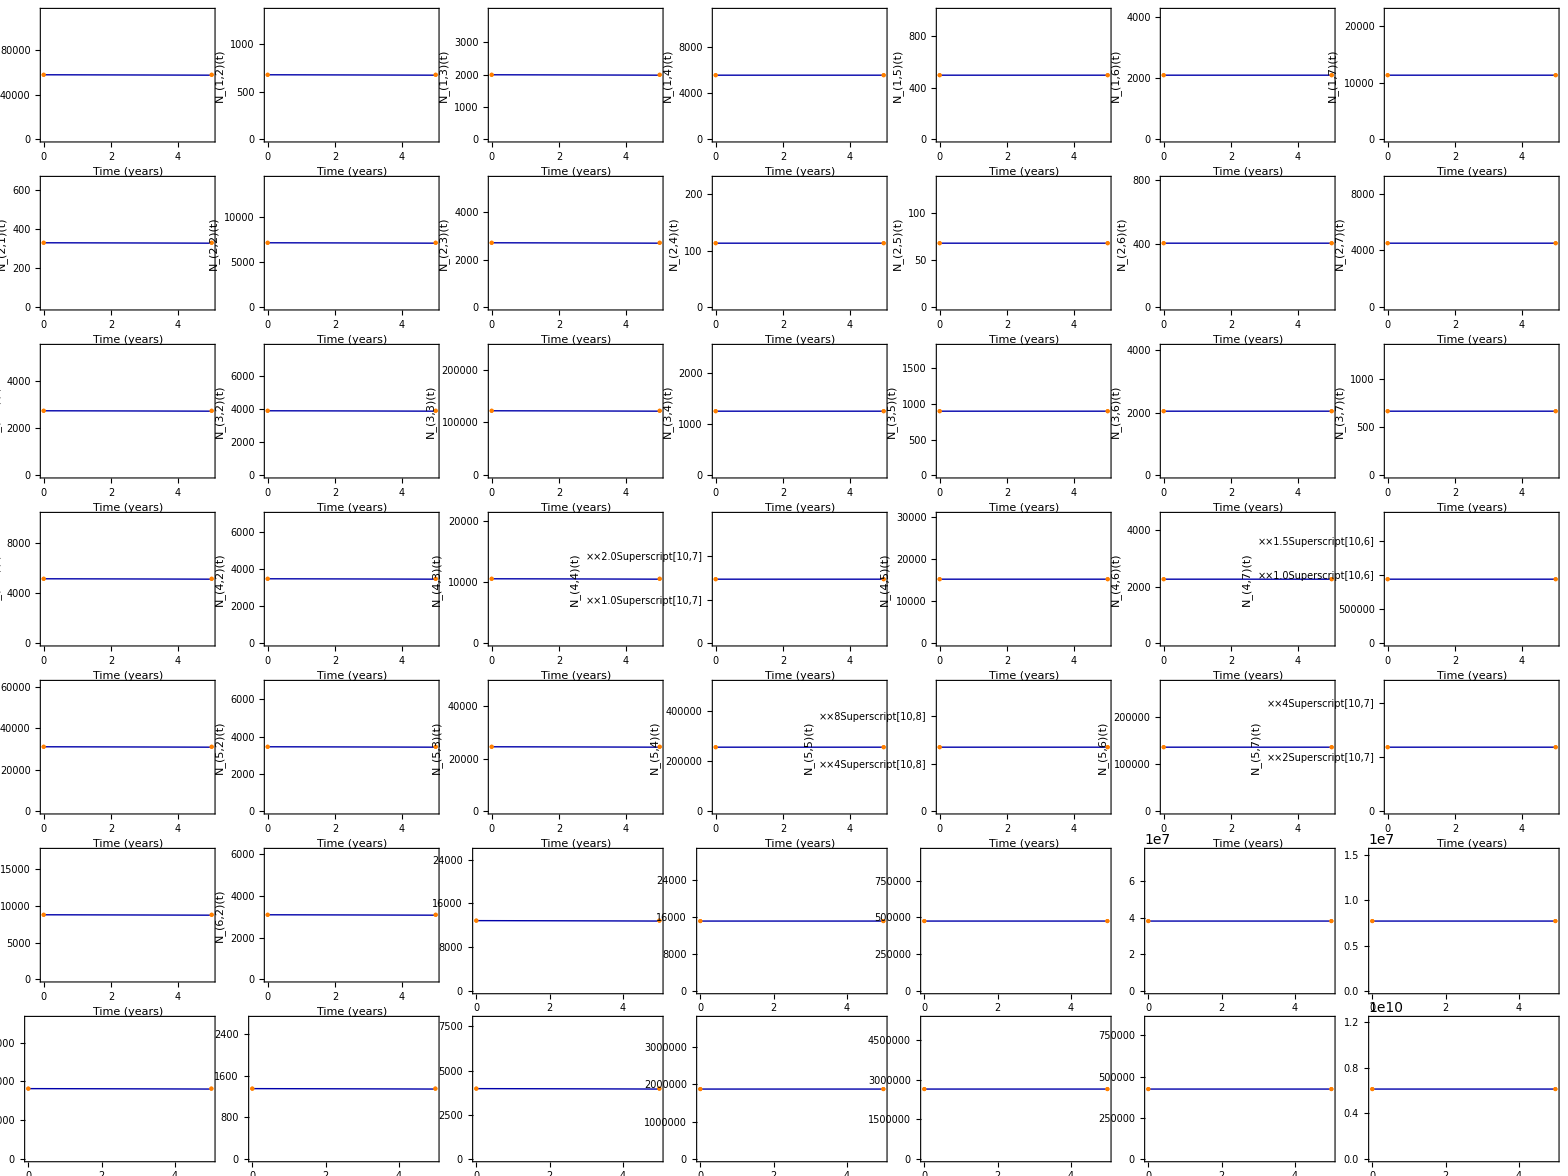

Plot number of individuals in different disease stages

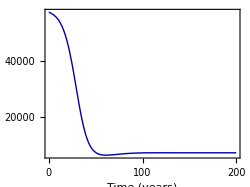
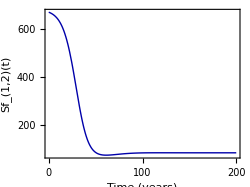
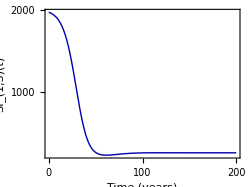
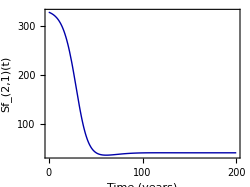
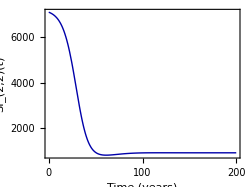
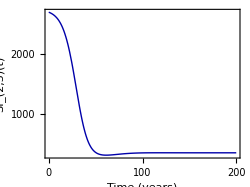
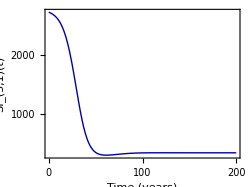
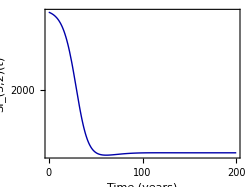

```mathematica
Print[Style["Parameters: 2020 + zero migration + infection",18,Orange,"Text"]]

PlotSolution[solution2020NoMigrationInfection,Subscript[t, start],Subscript[t, end],DemographyMatrix2020,DemographyMatrix2020]

Print[Style["Plot number of individuals in different disease stages",18,Blue,"Text"]]
Table[Plot[{Evaluate[VarsList⟦i⟧/.solution2020NoMigrationInfection]},{t,Subscript[t, start],Subscript[t, endsteady]},AspectRatio->0.75,ImageSize->250,PlotRangePadding->{{0,0.075},{0,Automatic}},PlotRange->{{0,Subscript[t, endsteady]},{0,All}},PlotStyle->{Thick,Darker[Blue]},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},PlotTheme-> "Web",FrameStyle->Directive[Black,17],(*PlotLabel->Style[Row[{intList⟦it⟧}],Black,17],*)FrameLabel-> {{VarsList⟦i⟧,None},{"Time (years)",None}}],{i,Length[VarsList]}]
```

```mathematica
Table[{i,j,((Subscript[NNf,i,j][t]/.solution2020NoMigrationInfection)/.t-> Subscript[t, start])⟦1⟧,DemographyMatrix2020⟦i,j⟧,((Subscript[NNf,i,j][t]/.solution2020NoMigrationInfection)/.t-> Subscript[t, endsteady])⟦1⟧},{i,Nationalities},{j,Nationalities}]
```

{{{1,1,57930.,57930,16528.5},{1,2,675.,675,192.59},{1,3,1992.,1992,568.355},{1,4,5554.,5554,5554.},{1,5,498.,498,498.},{1,6,2102.,2102,2102.},{1,7,11310.,11310,11310.}},{{2,1,331.,331,94.4405},{2,2,7185.,7185,2050.01},{2,3,2722.,2722,776.637},{2,4,113.,113,113.},{2,5,68.,68,68.},{2,6,403.,403,403.},{2,7,4511.,4511,4511.}},{{3,1,2745.,2745,783.2},{3,2,3909.,3909,1115.31},{3,3,122079.,122079,34831.4},{3,4,1259.,1259,1259.},{3,5,899.,899,899.},{3,6,2043.,2043,2043.},{3,7,665.,665,665.}},{{4,1,5128.,5128,1463.11},{4,2,3486.,3486,994.621},{4,3,10562.,10562,3013.54},{4,4,1.4667×10^7,14667013,1.4667×10^7},{4,5,15216.,15216,15216.},{4,6,2260.,2260,2260.},{4,7,937237.,937237,937237.}},{{5,1,31129.,31129,8881.68},{5,2,3459.,3459,986.917},{5,3,24432.,24432,6970.91},{5,4,257024.,257024,257024.},{5,5,5.41021×10^8,541020882,5.41021×10^8},{5,6,135683.,135683,135683.},{5,7,2.35932×10^7,23593243,2.35932×10^7}},{{6,1,8812.,8812,2514.23},{6,2,3098.,3098,883.917},{6,3,12848.,12848,3665.77},{6,4,15122.,15122,15122.},{6,5,474863.,474863,474863.},{6,6,3.82308×10^7,38230755,3.82308×10^7},{6,7,7.70451×10^6,7704507,7.70451×10^6}},{{7,1,3625.,3625,1034.28},{7,2,1353.,1353,386.036},{7,3,3975.,3975,1134.14},{7,4,1.87487×10^6,1874872,1.87487×10^6},{7,5,2.64061×10^6,2640610,2.64061×10^6},{7,6,424205.,424205,424205.},{7,7,6.14199×10^9,6141989658,6.14199×10^9}}}